```mathematica
Quit[]
```

## Grand Hatsuda-Okazaki

Follow 2208.01426 (4.2).

### Test θ derivative formula (3.10)

```mathematica
tmp=ⅈ q^(-1/8) D[EllipticTheta[1,Log[u]/(2ⅈ),Sqrt[q]],u]/.u->1
```

EllipticThetaPrime[1,0,√q]/(2 q^(1/8))

```mathematica
tmp/(q^(-1/8)DedekindEta[Log[q]/(2π ⅈ)]^3)/.q->Exp[-π]//N
```

1.

```mathematica
Series[tmp^(1/3),{q,0,5}]
```

1-q-q^2+q^5+O[q]^(41/8)

```mathematica
Series[q^(-1/24)DedekindEta[Log[q]/(2π ⅈ)],{q,0,5}]
```

1-q-q^2+q^5+O[q]^(121/24)

### Grand u=1

```mathematica
S[expr_]:=Simplify[expr,Assumptions->{u>0,ξ>0,b>0,q>0}];
```

```mathematica
cut=4;
NN=2;
θ[u_,q_]:=-u^(-1/2)QPochhammer[q,q]QPochhammer[u,q]QPochhammer[q u^-1,q];
Λ[N_,ξ_,q_]:=(-1)^N ξ^(N^2/2)QPochhammer[q,q]^3/θ[ξ^-N,q](*(q^(-1/8)DedekindEta[Log[q]/(2π ⅈ)]^3)*);
(*Λq[N_,b_,q_]:=Series[Λ[N,b,q],{q,0,cut}];*)
Series[Λ[NN,q^-1ξ^-1,q]/((-1)^(-NN )Λ[NN,ξ,q]),{q,0,cut}]//PowerExpand
```

-1+O[q]^5

```mathematica
(*Ξ[μ_,ξ_,q_]:=μ Product[1-μ ξ^-p/(1-q^p),{p,1,4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}]*Product[1-μ ξ^-p/(1-q^p),{p,-4Max[cut,Ceiling[1/4 NN √(1+8 cut)]],-1}];*)
Ξ[μ_,ξ_,q_]:=μ Product[(1-μ ξ^-p/(1-q^p))(1+μ ξ^p q^p/(1-q^p)),{p,1,4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];
```

```mathematica
Series[Ξ[μ,ξ,q]/Ξ[-μ,ξ^-1q^-1,q],{q,0,cut}]
```

-1

```mathematica
Z[N_,ξ_,q_]:=SeriesCoefficient[Ξ[μ,ξ,q],{μ,0,N}];
Series[(-1)^NN Z[NN,ξ,q]/Z[NN,ξ^-1q^-1,q],{q,0,cut}]//S
```

-1+O[q]^5

```mathematica
II[N_,ξ_,q_]:=Λ[N,ξ,q]Z[N,ξ,q];
```

```mathematica
Series[II[NN,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+(3+5/b^8+5 b^8) x^8+O[x]^9

```mathematica
NN=3;
cut=2;
```

```mathematica
tmp1=Series[Λ[NN,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
tmp2=Series[Z[NN,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
tmp3=Series[II[NN,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

-1/x^2-(1+b^6)/(b^3 x)+(1-1/b^6-b^6)-((1+b^18) x)/b^9-((1+b^24) x^2)/b^12+(-1/b^15+1/b^3+b^3-b^15) x^3-((1+b^18+b^36) x^4)/b^18+O[x]^5

-x^2+((-1+b^2)^2 (1+b^2) x^3)/b^3+(-3+1/b^4-1/b^2-b^2+b^4) x^4+O[x]^5

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(3/b^3+1/b+b+3 b^3) x^3+(1+4/b^4+4 b^4) x^4+O[x]^6

```mathematica
cut=7;
ω[μ_,x_]:=Product[1+μ x^p/(1-x^(2p)),{p,1,2cut}];
ν[μ_,x_]:=Product[(1+μ x^p)/(1-x^(2p)),{p,1,2cut}];
Ω[μ_,x_]:=μ ω[μ,x]^2;
Ω[μ_,x_]:=μ ν[μ,x]^2;
```

```mathematica
-Exponent[#,x^-1]&/@CoefficientList[Series[Ω[μ,x],{μ,0,cut},{x,0,2cut}],μ][[2;;]]
```

{0,1,2,4,6,9,12}

```mathematica
-Exponent[#,x^-1]&/@CoefficientList[Series[ω[μ,x],{μ,0,cut},{x,0,2cut}],μ][[1;;]]
```

{0,1,3,6,10}

```mathematica
-Exponent[#,x^-1]&/@CoefficientList[Series[ν[μ,x],{μ,0,cut},{x,0,2cut}],μ][[1;;]]
```

{0,1,3,6,10}

```mathematica
Series[ω[μ,x],{μ,0,cut},{x,0,2cut}]
```

1+(x+x^2+2 x^3+x^4+2 x^5+2 x^6+2 x^7+x^8+3 x^9+2 x^10+2 x^11+2 x^12+2 x^13+2 x^14+O[x]^15) μ+(x^3+x^4+3 x^5+3 x^6+6 x^7+5 x^8+9 x^9+9 x^10+13 x^11+11 x^12+17 x^13+16 x^14+O[x]^15) μ^2+(x^6+x^7+3 x^8+4 x^9+8 x^10+9 x^11+16 x^12+17 x^13+27 x^14+O[x]^15) μ^3+(x^10+x^11+3 x^12+4 x^13+9 x^14+O[x]^15) μ^4+O[x]^15 μ^5+O[x]^21 μ^6+O[x]^28 μ^7+O[μ]^8

```mathematica
Series[ν[μ,x],{μ,0,cut},{x,0,2cut}]
```

(1+x^2+2 x^4+3 x^6+5 x^8+7 x^10+11 x^12+15 x^14+O[x]^15)+(x+x^2+2 x^3+2 x^4+4 x^5+4 x^6+7 x^7+7 x^8+12 x^9+12 x^10+19 x^11+19 x^12+30 x^13+30 x^14+O[x]^15) μ+(x^3+x^4+3 x^5+3 x^6+7 x^7+7 x^8+14 x^9+14 x^10+26 x^11+26 x^12+45 x^13+45 x^14+O[x]^15) μ^2+(x^6+x^7+3 x^8+4 x^9+8 x^10+10 x^11+18 x^12+22 x^13+36 x^14+O[x]^15) μ^3+(x^10+x^11+3 x^12+4 x^13+9 x^14+O[x]^15) μ^4+O[x]^15 μ^5+O[x]^21 μ^6+O[x]^28 μ^7+O[μ]^8

```mathematica
tmp1*tmp2//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(3/b^3+1/b+b+3 b^3) x^3+(2+5/b^4+1/b^2+b^2+5 b^4) x^4+O[x]^5

```mathematica
U[μ_,ξ_,q_]:=μ Product[(1+μ ξ^-p/(1-q^p))(1+μ ξ^p q^p/(1-q^p)),{p,1,4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];
```

```mathematica
Series[U[NN,ξ,q]/.ξ->q^(-1/2)b/.b->1/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+2 x+3 x^2+8 x^3+11 x^4+20 x^5+35 x^6+52 x^7+82 x^8+O[x]^9

```mathematica
ans1=Series[II[NN,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(-1+1/b^2+b^2) x^2+(1/b^3+b^3) x^3+(1/b^4+b^4) x^4+(1/b^5-1/b-b+b^5) x^5+(1+1/b^6+b^6) x^6+(1/b^7+b^7) x^7+(1/b^8-1/b^2-b^2+b^8) x^8+O[x]^9

```mathematica
ans2/ans1//S
```

1+(1+1/b^2+b^2) x^2-(2 (1+b^2) x^3)/b+((1+b^2+b^4)^2 x^4)/b^4-(2 (1+2 b^2+2 b^4+b^6) x^5)/b^3+(6+1/b^6+2/b^4+5/b^2+5 b^2+2 b^4+b^6) x^6-(2 ((1+b^2) (1+b^2+b^4)^2) x^7)/b^5+((1+b^2)^2 (1+5 b^4+3 b^6+5 b^8+b^12) x^8)/b^8+O[x]^9

### Grand u=x

```mathematica
S[expr_]:=Simplify[expr,Assumptions->{u>0,ξ>0,b>0,q>0}];
```

```mathematica
cut=10;
NN=4;
θ[u_,q_]:=-u^(-1/2)QPochhammer[q,q]QPochhammer[u,q]QPochhammer[q u^-1,q];
Λ[N_,u_,ξ_,q_]:=(-1)^N ξ^(N^2/2)θ[u,q]/θ[u ξ^(-N),q];
Λx[N_,b_,x_]:=(-1)^N (b/x)^(N(N-1)/2)QPochhammer[x,x^2]^2/(QPochhammer[b^N x^(1-N),x^2]QPochhammer[b^-N x^(N+1),x^2]);
Λx[N_,b_,x_]:=(-1)^N (b/x)^(N^2/2)θ[x,x^2]/θ[b^-N x^(N+1),x^2];
```

```mathematica
tmp1=Series[Λ[NN,q^(1/2),ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify;
```

```mathematica
Series[Λx[NN,b,x],{x,0,2cut}]//S//PowerExpand//Simplify;
```

```mathematica
Ξ[μ_,u_,ξ_,q_]:=Product[1-μ ξ^-p/(1-u q^p),{p,-2Max[cut,Ceiling[1/4 NN √(1+8 cut)]],2Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];
Z[N_,u_,ξ_,q_]:=SeriesCoefficient[Ξ[μ,u,ξ,q],{μ,0,N}];
Ξ[μ_,b_,x_]:=Product[(1-μ b^-p x^p/(1-x^(2p+1))),{p,-4Max[cut,Ceiling[1/4 NN √(1+8 cut)]],4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];
Ξ[μ_,b_,x_]:=Product[(1-μ b^-p x^p/(1-x^(2p+1))),{p,0,4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}]*Product[(1+μ b^p x^(p-1)/(1-x^(2p-1))),{p,1,4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];
Ξ[μ_,b_,x_]:=(1-μ/(1-x))(1+μ b/(1-x))Product[(1-μ b^-p x^p/(1-x^(2p+1)))(1+μ b^(p+1) x^p/(1-x^(2p+1))),{p,1,4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];(*Product[(1+μ b^(p+1) x^p/(1-x^(2p+1))),{p,1,4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];*)
Z[N_,b_,x_]:=SeriesCoefficient[Ξ[μ,b,x],{μ,0,N}];
```

```mathematica
tmp2=Series[Z[NN,b,x],{x,0,2cut}]//S//PowerExpand//Simplify;
```

```mathematica
tmp2
```

-b+(-1+1/b-2 b-b^2+b^3) x+(-1+1/b^2-4 b-b^2+b^4) x^2+2 (-1+1/b^3-2 b-b^2+b^5) x^3+2 (-1+1/b^4-3 b-b^2+b^6) x^4+(-3+3/b^5-1/b^2+1/b-8 b-3 b^2+b^3-b^4+3 b^7) x^5+(-3+3/b^6-8 b-3 b^2+3 b^8) x^6+4 (-1+1/b^7-2 b-b^2+b^9) x^7+(-4+4/b^8-13 b-4 b^2+4 b^10) x^8+O[x]^9

```mathematica
tmp1*tmp2//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+(3+5/b^8+5 b^8) x^8+O[x]^9

```mathematica
Series[Z[NN,b,x],{x,0,2cut}]//S//PowerExpand//Simplify
```

```mathematica
(*Series[Λx[NN,b,x],{x,0,2cut}]//S//PowerExpand//Simplify;*)
```

```mathematica
Z[N_,ξ_,q_]:=SeriesCoefficient[Ξ[μ,ξ,q],{μ,0,N}];
Series[(-1)^NN Z[NN,ξ,q]/Z[NN,ξ^-1q^-1,q],{q,0,cut}]//S
```

-1+O[q]^5

```mathematica
II[N_,ξ_,q_]:=Λ[N,ξ,q]Z[N,ξ,q];
```

```mathematica
Series[II[NN,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+(3+5/b^8+5 b^8) x^8+O[x]^9

```mathematica
NN=2;
cut=2;
```

```mathematica
tmp1=Series[Λ[NN,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
tmp2=Series[Z[NN,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
tmp3=Series[II[NN,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

b/((-1+b^2) x)+(-1/b+b) x+((-1+b^6) x^3)/b^3+O[x]^5

(-1/b+b) x+((-1+b^4) x^2)/b^2+((-1+b^2) (1+b^2)^2 x^3)/b^3+((-1+b^8) x^4)/b^4+O[x]^5

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+O[x]^5

```mathematica
tmp1*tmp2//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(3/b^3+1/b+b+3 b^3) x^3+(2+5/b^4+1/b^2+b^2+5 b^4) x^4+O[x]^5

```mathematica
U[μ_,ξ_,q_]:=μ Product[(1+μ ξ^-p/(1-q^p))(1+μ ξ^p q^p/(1-q^p)),{p,1,4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];
```

```mathematica
Series[U[NN,ξ,q]/.ξ->q^(-1/2)b/.b->1/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+2 x+3 x^2+8 x^3+11 x^4+20 x^5+35 x^6+52 x^7+82 x^8+O[x]^9

```mathematica
ans1=Series[II[NN,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(-1+1/b^2+b^2) x^2+(1/b^3+b^3) x^3+(1/b^4+b^4) x^4+(1/b^5-1/b-b+b^5) x^5+(1+1/b^6+b^6) x^6+(1/b^7+b^7) x^7+(1/b^8-1/b^2-b^2+b^8) x^8+O[x]^9

```mathematica
ans2/ans1//S
```

1+(1+1/b^2+b^2) x^2-(2 (1+b^2) x^3)/b+((1+b^2+b^4)^2 x^4)/b^4-(2 (1+2 b^2+2 b^4+b^6) x^5)/b^3+(6+1/b^6+2/b^4+5/b^2+5 b^2+2 b^4+b^6) x^6-(2 ((1+b^2) (1+b^2+b^4)^2) x^7)/b^5+((1+b^2)^2 (1+5 b^4+3 b^6+5 b^8+b^12) x^8)/b^8+O[x]^9

### Grand general u

```mathematica
S[expr_]:=Simplify[expr,Assumptions->{u>0,ξ>0,b>0,q>0}];
```

```mathematica
cut=4;
NN=2;
```

```mathematica
θ[u_,q_]:=-u^(-1/2)QPochhammer[q,q]QPochhammer[u,q]QPochhammer[q u^-1,q];
Λ[N_,u_,ξ_,q_]:=(-1)^N ξ^(N^2/2)θ[u,q]/θ[u ξ^(-N),q];
Series[(-1)^(NN+1)ξ^(-NN^2/2)Λ[NN,ξ^(NN/2),ξ,q],{q,0,cut}]//PowerExpand
Series[Λ[NN,u^-1,q^-1ξ^-1,q]/((-u)^(-NN )Λ[NN,u,ξ,q]),{q,0,cut}]//PowerExpand
```

1+O[q]^5

1+O[q]^5

```mathematica
Λ[NN,u^-1,q^-1ξ^-1,q]/((-u)^(-NN )Λ[NN,u,ξ,q])/.{u->Exp[-π/2],ξ->Exp[-2π],q->Exp[-π]}//N
```

1.

```mathematica
(* Range: see (3.4) *)
Ξ[μ_,u_,ξ_,q_]:=Product[1-μ ξ^-p/(1-u q^p),{p,-2Max[cut,Ceiling[1/4 NN √(1+8 cut)]],2Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];
Series[Ξ[μ,u,ξ,q]/Ξ[-u^-1μ,u^-1,ξ^-1q^-1,q],{q,0,cut}]
```

1+O[q]^5

```mathematica
Z[N_,u_,ξ_,q_]:=SeriesCoefficient[Ξ[μ,u,ξ,q],{μ,0,N}];
Series[(-u)^NN Z[NN,u,ξ,q]/Z[NN,u^-1,ξ^-1q^-1,q],{q,0,cut}]//S
```

1+O[q]^5

```mathematica
II[N_,u_,ξ_,q_]:=Λ[N,u,ξ,q]Z[N,u,ξ,q];
```

```mathematica
Series[II[NN,u,ξ,q]/.u->ξ^(NN/2)/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+(3+5/b^8+5 b^8) x^8+O[x]^10

```mathematica
Series[II[NN,u,ξ,q]/.u->-1/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+(2+4/b^8+1/b^6-1/b^4+1/b^2+b^2-b^4+b^6+4 b^8) x^8+O[x]^9

```mathematica
Series[II[NN,u,ξ,q]/.u->1/2/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+((4-10 b^2+3 b^8-6 b^10+5 b^16-8 b^18) x^8)/(b^8-2 b^10)+O[x]^9

```mathematica
Series[II[NN,u,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+((5 b^2+3 b^10+4 b^18-4 u-3 b^8 u-5 b^16 u) x^8)/(b^10-b^8 u)+O[x]^9

```mathematica
Series[Z[NN,u,ξ,q]/.u->ξ^(NN/2),{q,0,cut}]
```

(-1-ξ^2-ξ^4-ξ^6-ξ^8-ξ^10-ξ^12-ξ^14)/((-1+ξ) ξ^15)-q/ξ+((-1-2 ξ^3) q^2)/ξ^3+((-1-ξ^4-2 ξ^6) q^3)/ξ^5+((-1-3 ξ^5-3 ξ^9) q^4)/ξ^7+O[q]^5

```mathematica
Series[(-1)^(NN+1)ξ^(NN^2/2)Z[NN,u,ξ,q]/.u->ξ^(NN/2)/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+(3+5/b^8+5 b^8) x^8+O[x]^9

```mathematica
n=2cut;
tmp=Series[1+Sum[indexGAP[2,i],{i,1,n}],{x,0,n}]//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+(3+5/b^8+5 b^8) x^8+O[x]^9

### Grand MacDonald u=1 (TODO)

```mathematica
S[expr_]:=Simplify[expr,Assumptions->{u>0,ξ>0,b>0,q>0}];
```

```mathematica
cut=2;
NN=2;
θ[u_,q_]:=-u^(-1/2)QPochhammer[q,q]QPochhammer[u,q]QPochhammer[q u^-1,q];
Λ[N_,b_,q_]:=(-1)^N ξ^(N^2/2)QPochhammer[q,q]^3/θ[ξ^-N,q](*(q^(-1/8)DedekindEta[Log[q]/(2π ⅈ)]^3)*);
(*Λq[N_,b_,q_]:=Series[Λ[N,b,q],{q,0,cut}];*)
Series[Λ[NN,q^-1ξ^-1,q]/((-1)^(-NN )Λ[NN,ξ,q]),{q,0,cut}]//PowerExpand
```

1

```mathematica
(*Ξ[μ_,ξ_,q_]:=μ Product[1-μ ξ^-p/(1-q^p),{p,1,4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}]*Product[1-μ ξ^-p/(1-q^p),{p,-4Max[cut,Ceiling[1/4 NN √(1+8 cut)]],-1}];*)
Ξ[μ_,ξ_,q_,s_]:=μ Product[(1-μ ξ^-p s^p/(1-q^p))(1+μ ξ^p q^p s^-p/(1-q^p)),{p,1,4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];
```

```mathematica
Z[N_,ξ_,q_,s_]:=SeriesCoefficient[Ξ[μ,ξ,q,s],{μ,0,N}];
```

```mathematica
II[N_,ξ_,q_,s_]:=Λ[N,ξ,q]Z[N,ξ,q,s];
```

```mathematica
Series[II[NN,ξ,q,s]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

(b^2-s^2)/((-1+b^2) s)+((b^4-s^4) x)/(b (-1+b^2) s^2)+((1+s^2) (b^6+b^2 s^2-b^4 s^2-s^4) x^2)/(b^2 (-1+b^2) s^3)+((-2 b^6 s^2+2 b^2 s^6+b^8 (1+s^2)-s^6 (1+s^2)+b^4 (s^2-s^6)) x^3)/(b^3 (-1+b^2) s^4)+((b^6 (s^2-s^4)-b^8 s^2 (2+s^4)+b^10 (1+s^2+s^4)-s^6 (1+s^2+s^4)+b^4 (s^6-s^8)+b^2 (s^4+2 s^8)) x^4)/(b^4 (-1+b^2) s^5)+O[x]^5

### Grand MacDonald general u (TODO)

```mathematica
S[expr_]:=Simplify[expr,Assumptions->{u>0,ξ>0,b>0,q>0,s>0}];
```

```mathematica
cut=2;
NN=2;
```

```mathematica
θ[u_,q_]:=-u^(-1/2)QPochhammer[q,q]QPochhammer[u,q]QPochhammer[q u^-1,q];
Λ[N_,u_,ξ_,q_]:=(-1)^N ξ^(N^2/2)θ[u,q]/θ[u ξ^(-N),q];
Series[(-1)^(NN+1)ξ^(-NN^2/2)Λ[NN,ξ^(NN/2),ξ,q],{q,0,cut}]//PowerExpand
Series[Λ[NN,u^-1,q^-1ξ^-1,q]/((-u)^(-NN )Λ[NN,u,ξ,q]),{q,0,cut}]//PowerExpand
```

1+O[q]^3

1+O[q]^3

```mathematica
(* Range: see (3.4) *)
Ξ[μ_,u_,ξ_,q_,s_]:=Product[1-μ ξ^-p s^p/(1-u q^p),{p,-2Max[cut,Ceiling[1/4 NN √(1+8 cut)]],2Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];
```

```mathematica
Z[N_,u_,ξ_,q_,s_]:=SeriesCoefficient[Ξ[μ,u,ξ,q,s],{μ,0,N}];
```

```mathematica
II[N_,u_,ξ_,q_,s_]:=Λ[N,u,ξ,q]Z[N,u,ξ,q,s];
```

```mathematica
Series[II[NN,u,ξ,q,s]/.u->ξ^(NN/2)/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

s+((s^2+s^3-s^4+b^2 (-1+s+s^2)) x)/(b s)+((s^3+s^4+s^5-s^6-b^2 s (-1+s^2)^2+b^4 (-1+s+s^2+s^3)) x^2)/(b^2 s^2)+((s^4+s^5+s^6+s^7-2 s^8+b^6 (-2+s+s^2+s^3+s^4)+b^4 (-s+s^3+s^4-s^6)+b^2 (-s^2+s^4+s^5-s^7)) x^3)/(b^3 s^3)+((-b^6 s (-1+s^2)^2 (1+s^2)-b^2 s^3 (-1+s^2)^2 (1+s^2)-b^4 s^2 (-1+s^2)^2 (1+s+s^2)+s^5 (1+s+s^2+s^3+s^4-2 s^5)+b^8 (-2+s+s^2+s^3+s^4+s^5)) x^4)/(b^4 s^4)+O[x]^6

```mathematica
Series[II[NN,u,ξ,q,s]/.u->-1/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

(b^2+s^2)/(s+b^2 s)+((b^2+s^2)^2 x)/((b+b^3) s^2)+((-b^6 (-3+s^2)-b^4 s^2 (-3+s^2)+b^2 s^2 (-1+3 s^2)+s^4 (-1+3 s^2)) x^2)/(b^2 (1+b^2) s^3)-((b^2+s^2)^2 (s^2+2 b^2 s^2-3 s^4+b^4 (-3+s^2)) x^3)/(b^3 (1+b^2) s^4)+((s^6-3 s^8+5 s^10+b^8 s^2 (6-4 s^2+s^4)+b^10 (5-3 s^2+s^4)+b^6 (-3 s^2+7 s^4-4 s^6)+b^4 (-4 s^4+7 s^6-3 s^8)+b^2 (s^4-4 s^6+6 s^8)) x^4)/(b^4 (1+b^2) s^5)+O[x]^5

### GAP

```mathematica
n=12;
tmp=Series[1+Sum[indexGAP[3,i],{i,1,n}],{x,0,n}]//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(3/b^3+1/b+b+3 b^3) x^3+(1+4/b^4+4 b^4) x^4+(5/b^5+1/b^3+1/b+b+b^3+5 b^5) x^5+(2+7/b^6+2/b^2+2 b^2+7 b^6) x^6+(8/b^7+1/b^5+1/b^3+2/b+2 b+b^3+b^5+8 b^7) x^7+(2 (5+b^4+b^6+b^8+b^10+b^12+5 b^16) x^8)/b^8+(12/b^9+1/b^7+1/b^5+1/b^3+2/b+2 b+b^3+b^5+b^7+12 b^9) x^9+(2 (7+b^4+b^6+2 b^8+b^10+2 b^12+b^14+b^16+7 b^20) x^10)/b^10+(16/b^11+1/b^9+1/b^7+2/b^5+3/b^3+3/b+3 b+3 b^3+2 b^5+b^7+b^9+16 b^11) x^11+(6+19/b^12+2/b^8+2/b^6+4/b^4+4 b^4+2 b^6+2 b^8+19 b^12) x^12+O[x]^13

```mathematica
n=12;
tmp=Series[1+Sum[indexGAP[2,i],{i,1,n}],{x,0,n}]//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+(3+5/b^8+5 b^8) x^8+(5/b^9+1/b^3+b^3+5 b^9) x^9+(6 (1+b^20) x^10)/b^10+(2 (3+b^10+b^12+3 b^22) x^11)/b^11+(7 (1+b^24) x^12)/b^12+O[x]^13

```mathematica
n=12;
tmp=Series[1+Sum[indexGAP[1,i],{i,1,n}],{x,0,n}]//Simplify
```

1+(1/b+b) x+(-1+1/b^2+b^2) x^2+(1/b^3+b^3) x^3+(1/b^4+b^4) x^4+(1/b^5-1/b-b+b^5) x^5+(1+1/b^6+b^6) x^6+(1/b^7+b^7) x^7+(1/b^8-1/b^2-b^2+b^8) x^8+(1/b^9+b^9) x^9+(1/b^10+b^10) x^10+(1/b^11-1/b^3+1/b+b-b^3+b^11) x^11+(-1+1/b^12+b^12) x^12+O[x]^13

### Grand u=1 (old)

```mathematica
cut=4;
NN=2;
(*θ[u_,q_]:=Series[ⅈ q^(-1/8)EllipticTheta[1,Log[u]/(2ⅈ),Sqrt[q]],{q,0,2cut+2}];*)
θ[u_,q_]:=-u^(-1/2)QPochhammer[q,q]QPochhammer[u,q]QPochhammer[q u^-1,q];
Λ[N_,b_,q_]:=(-1)^N ξ^(N^2/2)(q^(-1/8)DedekindEta[Log[q]/(2π ⅈ)]^3)/θ[ξ^-N,q]/.ξ->q^(-1/2)b(*//TrigToExp*);
Λq[N_,b_,q_]:=Series[Λ[N,b,q],{q,0,cut}];
```

```mathematica
tmp1=Simplify[Λq[NN,b,q],Assumptions->{b>0,q>0}];
```

```mathematica
Ξ[μ_,b_,q_]:=μ Product[1-μ ξ^-p/(1-q^p),{p,1,2cut}]Product[1-μ ξ^-p/(1-q^p),{p,-2cut,-1}]/.ξ->q^(-1/2)b;
```

```mathematica
tmp2=1+Series[SeriesCoefficient[Ξ[μ,b,q],{μ,0,NN}],{q,0,cut}];
```

```mathematica
Series[Normal[Series[(-x(1-b^2)/b)tmp1*tmp2,{q,0,cut}]]/.q->x^2//PowerExpand,{x,0,2cut},{b,0,10}]
```

1+(-1/b+b+O[b]^11) x+(-2+2 b^2+O[b]^11) x^2+(-2/b^3+2/b-2 b+2 b^3+O[b]^11) x^3+(-1/b^4+1/b^2-3 b^2+3 b^4+O[b]^11) x^4+(-3/b^5+3/b^3-3 b^3+3 b^5+O[b]^11) x^5+(-2/b^6+2/b^4-2/b^2+2-4 b^4+4 b^6+O[b]^11) x^6+(-4/b^7+4/b^5-4 b^5+4 b^7+O[b]^11) x^7+(-3/b^8+3/b^6-5 b^6+5 b^8+O[b]^11) x^8+O[x]^9

```mathematica
-x^2 Series[Normal[Series[tmp1*tmp2,{q,0,cut}]]/.q->x^2//PowerExpand,{x,0,2cut},{b,0,10}]
```

(b+b^3+b^5+b^7+b^9+O[b]^11) x-x^2+(-2 b+O[b]^11) x^3+(-2/b^2-2 b^2+O[b]^11) x^4+(-1/b^3-3 b^3+O[b]^11) x^5+(-3/b^4-3 b^4+O[b]^11) x^6+(-2/b^5-2/b-4 b^5+O[b]^11) x^7+(-4/b^6-4 b^6+O[b]^11) x^8+(-3/b^7-5 b^7+O[b]^11) x^9+O[x]^11

### Grand general u (wrong)

```mathematica
cut=10;
NN=2;
Ξ[μ_,u_,ξ_,q_]:=Product[1-μ ξ^-p/(1-u q^p),{p,-cut,cut}];
```

```mathematica
(*θ[u_,q_]:=Series[ⅈ q^(-1/8)EllipticTheta[1,Log[u]/(2ⅈ),Sqrt[q]],{q,0,2cut+2}];*)
θ[u_,q_]:=-u^(-1/2)QPochhammer[q,q]QPochhammer[u,q]QPochhammer[q u^-1,q];
Λ[N_,u_,b_,q_]:=(-1)^N ξ^(N^2/2)θ[u,q]/θ[u ξ^(-N),q]/.ξ->q^(-1/2)b(*//TrigToExp*);
Λq[N_,u_,b_,q_]:=S[Series[Λ[N,u,b,q],{q,0,cut}]];
Ξ[μ_,u_,b_,q_]:=Product[1-μ ξ^-p/(1-u q^p),{p,-2cut,2cut}]/.ξ->q^(-1/2)b;
Z[N_,u_,b_,q_]:=SeriesCoefficient[Ξ[μ,u,ξ,q],{μ,0,N}];
(*II[N_,u_,b_,q_]:=Λq[N,u,b,q]SeriesCoefficient[Ξ[μ,u,b,q],{μ,0,N}];*)
```

```mathematica
tmp1=Λq[NN,u,b,q];
tmp2=1+Series[SeriesCoefficient[Ξ[μ,u,b,q],{μ,0,NN}],{q,0,cut}];
```

```mathematica
tmp1*tmp2//S
```

u+(b (2-1/u)+(1-u+u^2)/b) √q+((u^2-u^4+u^5+b^4 (-1+u+u^2)-b^2 u (-1+3 u-2 u^2+u^3)) q)/(b^2 u^2)+((-b^4 (-1+u)^3 u+u^3-b^2 (-1+u)^3 u^3-u^6+u^7+b^6 (-1+u+u^3)) q^(3/2))/(b^3 u^3)+((-b^6 (-1+u)^3 u-2 b^4 (-1+u)^3 u^3+u^4-b^2 (-1+u)^3 u^5-u^8+u^9+b^8 (-1+u+u^4)) q^2)/(b^4 u^4)+(b (7+3/u^2-8/u-3 u)-(b^3 (-1+u)^3)/u^4-((-1+u)^3 u^2)/b^3+(2-8 u+8 u^2-3 u^3)/b+(b^5 (-1+u+u^5))/u^5+(1-u^5+u^6)/b^5) q^(5/2)+(-13-(b^4 (-1+u)^3)/u^5-(3 b^2 (-1+u)^3)/u^3-1/u^2+6/u+14 u-(3 (-1+u)^3 u)/b^2-6 u^2+u^3-((-1+u)^3 u^3)/b^4+(b^6 (-1+u+u^6))/u^6+(1-u^6+u^7)/b^6) q^3+O[q]^(13/4)

### Grand (old)

```mathematica
cut=2;
θ[u_,q_]:=Series[ⅈ q^(-1/8)EllipticTheta[1,Log[u]/(2ⅈ),Sqrt[q]],{q,0,cut+2}];
ξ^(1/2)*(q^(-1/8)DedekindEta[Log[q]/(2π ⅈ)]^3)/θ[ξ,q]//TrigToExp//Simplify
```

ξ/(-1+ξ)+(-1+ξ) q+((-1+ξ^3) q^2)/ξ+O[q]^3

```mathematica
cut=2;
(*θ[u_,q_]:=Series[ⅈ q^(-1/8)EllipticTheta[1,Log[u]/(2ⅈ),Sqrt[q]],{q,0,cut+2}];*)
θ[u_,q_]:=ⅈ q^(-1/8)EllipticTheta[1,Log[u]/(2ⅈ),Sqrt[q]];
Λ[N_,u_,ξ_,q_]:=(-1)^N ξ^(N^2/2)θ[u,q]/θ[u ξ^-N,q];
(*Ξ[μ_,u_,ξ_,q_]:=(1-μ/(1-u))Product[(1-μ ξ^-p/(1-u q^p))(1+μ u^-1 ξ^p q^p/(1-u^-1q^p)),{p,1,cut}];*)
Ξ[μ_,u_,ξ_,q_]:=Product[1-μ ξ^-p/(1-u q^p),{p,-cut,cut}];
II[N_,u_,ξ_,q_]:=Λ[N,u,ξ,q]SeriesCoefficient[Ξ[μ,u,ξ,q],{μ,0,N}]//Simplify;
```

```mathematica
tmp=Series[II[1,u,ξ,q]/.{ξ->q^(-1/2)t^2},{q,0,cut}];
```

$Aborted

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

ξ/(-1+ξ)+(-1+ξ) q+((-1+ξ^3) q^2)/ξ+O[q]^3

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

ξ/(-1+ξ)+(-1+ξ) q+((-1+ξ^3) q^2)/ξ+(1-1/ξ^2-ξ+ξ^3) q^3+O[q]^4

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

ξ/(-1+ξ)+(-1+ξ) q+((-1+ξ^3) q^2)/ξ+(1-1/ξ^2-ξ+ξ^3) q^3+((-1+ξ^7) q^4)/ξ^3+O[q]^5

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

ξ/(-1+ξ)+(-1-1/ξ+ξ) q-((1+ξ+ξ^3+ξ^4-ξ^5) q^2)/ξ^3+O[q]^3

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

(1+ξ^2)/((-1+ξ) ξ)+((-1-ξ+ξ^4) q)/ξ^3-((1+ξ+ξ^2+ξ^3+ξ^5-2 ξ^7) q^2)/ξ^5+O[q]^3

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

(1+ξ^2+ξ^4+ξ^6)/((-1+ξ) ξ^5)+((-1-ξ+ξ^8) q)/ξ^7-((1+ξ+ξ^2+ξ^3+ξ^4+ξ^5-ξ^8-2 ξ^11) q^2)/ξ^9+O[q]^3

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

(1+ξ+ξ^2)/(-1+ξ^2)+((-1-ξ+ξ^3) q)/ξ^2-((1+ξ+ξ^2+ξ^4+ξ^5-2 ξ^6) q^2)/ξ^4-((1+ξ+ξ^2+ξ^6+ξ^8-ξ^9) q^3)/ξ^6+O[q]^4

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

(1+ξ^2+ξ^4)/((-1+ξ) ξ^3)+((-1-ξ+ξ^6) q)/ξ^5-((1+ξ+ξ^2+ξ^3+ξ^4+ξ^5-ξ^6-2 ξ^9) q^2)/ξ^7-((1+ξ+ξ^2+ξ^3+ξ^7+ξ^8+ξ^9-ξ^10-2 ξ^12) q^3)/ξ^9+O[q]^4

## Residue method

### 1/16 unrefined index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_]:=1-(1-x^2)^3/(1-x^3)^2

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=2;
LL=30;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)]
```

{0.390262,1+6 x^4-6 x^5-7 x^6+18 x^7+6 x^8-36 x^9+6 x^10+84 x^11-80 x^12-132 x^13+309 x^14-18 x^15-567 x^16+516 x^17+613 x^18-1392 x^19-180 x^20+2884 x^21-1926 x^22-4242 x^23+7890 x^24+792 x^25-15876 x^26+13804 x^27+15177 x^28-37536 x^29+7049 x^30+O[x]^31}

```mathematica
NN=3;
LL=30;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)]
```

{1.90819,1+6 x^4-6 x^5+3 x^6+6 x^7-16 x^9+27 x^10+18 x^11-87 x^12+96 x^13+54 x^14-222 x^15+132 x^16+210 x^17-235 x^18-468 x^19+1284 x^20-534 x^21-2268 x^22+4392 x^23-1995 x^24-4128 x^25+6957 x^26-1288 x^27-5310 x^28-2376 x^29+22695 x^30+O[x]^31}

```mathematica
NN=4;
LL=15;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)]
```

{0.527629,1+6 x^4-6 x^5+3 x^6+6 x^7+15 x^8-36 x^9+24 x^10+36 x^11-37 x^12-30 x^13+78 x^14+88 x^15+O[x]^16}

### 1/16 index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_,a_,b_,u_,v_,w_]:=1-((1-u x^2)(1-v x^2)(1-w x^2))/((1-a x^3)(1-b x^3))

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j,a^j,b^j,u^j,v^j,w^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=2;
LL=32;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)//Simplify]
```

```mathematica
DumpSave[NotebookDirectory[]<>"grav16_2_32.mx",tmp];
```

```mathematica
NN=2;
LL=32;
Get[NotebookDirectory[]<>"grav16_2_32.mx"];
```

```mathematica
NN=3;
LL=28;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)//Simplify]
```

```mathematica
DumpSave[NotebookDirectory[]<>"grav16_3_28.mx",tmp];
```

```mathematica
NN=4;
LL=24;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)//Simplify]
```

### 1/16 BMN index

```mathematica
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]
```

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_,u_,v_,w_]:=1-(1-u x^2)(1-v x^2)(1-w x^2)

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j,u^j,v^j,w^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=24;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)//Simplify]
```

{0.85428,1+(u^2+v^2+v w+w^2+u (v+w)) x^4+(u^3+v^3-u v w+w^3) x^6+(u^4+v^4+v^2 w^2+w^4+u v w (v+w)+u^2 (v^2+v w+w^2)) x^8+(u^5+v^5+v^4 w+v w^4+w^5+u^4 (v+w)-2 u^2 v w (v+w)+u (v^2-w^2)^2) x^10+(2 u^6+2 v^6-2 u^4 v w+u^2 v^2 w^2+v^3 w^3+2 w^6+u^3 (v^3+w^3)-2 u v w (v^3+w^3)) x^12+(u^7+v^7+v^5 w^2+v^2 w^5+w^7+u^4 v w (v+w)-u^3 v w (v^2+w^2)+u^5 (v^2+v w+w^2)+u v w (v^4+v^3 w-v^2 w^2+v w^3+w^4)+u^2 (v^5+v^4 w+v w^4+w^5)) x^14+(2 u^8+2 v^8+v^7 w+v^4 w^4+v w^7+2 w^8+u^7 (v+w)-2 u^5 v w (v+w)+u (v-w)^2 (v+w)^3 (v^2-v w+w^2)-u^2 v w (v+w)^2 (2 v^2-3 v w+2 w^2)+u^3 v w (v^3+2 v^2 w+2 v w^2+w^3)+u^4 (v^4+v^3 w-v^2 w^2+v w^3+w^4)) x^16+(2 u^9+2 v^9-2 u^7 v w+v^6 w^3+v^3 w^6+2 w^9+u^5 v w (v^2+3 v w+w^2)-2 u^4 v w (v^3+w^3)+u^6 (v^3+v^2 w+v w^2+w^3)+u^2 v w (v^5+3 v^4 w+3 v w^4+w^5)+u v w (-2 v^6+v^5 w+v^4 w^2-2 v^3 w^3+v^2 w^4+v w^5-2 w^6)+u^3 (v^6+v^5 w-v^3 w^3+v w^5+w^6)) x^18+(2 u^10+2 v^10+v^8 w^2+v^5 w^5+v^2 w^8+2 w^10+u^7 v w (v+w)+u^5 (v-w)^2 (v+w)^3+u^8 (v^2+v w+w^2)-2 u^6 v w (v^2+v w+w^2)+u^4 v w (v^4-3 v^2 w^2+w^4)-u^3 v w (2 v^5+2 v^4 w+3 v^3 w^2+3 v^2 w^3+2 v w^4+2 w^5)+u^2 (v+w)^2 (v^6-v^5 w-v^4 w^2+v^3 w^3-v^2 w^4-v w^5+w^6)+u v w (v^7+v^6 w-2 v^5 w^2+v^4 w^3+v^3 w^4-2 v^2 w^5+v w^6+w^7)) x^20+(2 u^11+2 v^11+v^10 w+v^7 w^4+v^4 w^7+v w^10+2 w^11+u^10 (v+w)-2 u^8 v w (v+w)+u^6 v w (v^3+v^2 w+v w^2+w^3)-2 u^5 v w (v^4+v^3 w+v w^3+w^4)+u^7 (v^4+v^3 w-v^2 w^2+v w^3+w^4)+u (v^2-w^2)^2 (v^6+v^3 w^3+w^6)+u^3 v w (v^6+v^5 w+v w^5+w^6)+u^4 (v^7+v^6 w-2 v^5 w^2-2 v^2 w^5+v w^6+w^7)-u^2 v w (2 v^7+v^6 w-v^5 w^2+2 v^4 w^3+2 v^3 w^4-v^2 w^5+v w^6+2 w^7)) x^22+(3 u^12+3 v^12-2 u^10 v w+v^9 w^3+v^6 w^6+v^3 w^9+3 w^12+u^8 v w (v+w)^2+u^9 (v^3+v^2 w+v w^2+w^3)-u^7 v w (2 v^3+v^2 w+v w^2+2 w^3)+u^5 v w (v^5+3 v^4 w+3 v^3 w^2+3 v^2 w^3+3 v w^4+w^5)+u^6 (v^6+v^5 w+v w^5+w^6)+u^4 (-2 v^7 w+3 v^5 w^3+3 v^4 w^4+3 v^3 w^5-2 v w^7)+u^2 v w (v^8+2 v^7 w-v^6 w^2+3 v^4 w^4-v^2 w^6+2 v w^7+w^8)+u v w (-2 v^9+v^8 w+v^7 w^2-2 v^6 w^3+v^5 w^4+v^4 w^5-2 v^3 w^6+v^2 w^7+v w^8-2 w^9)+u^3 (v^9+v^8 w-v^7 w^2+3 v^5 w^4+3 v^4 w^5-v^2 w^7+v w^8+w^9)) x^24+O[x]^25}

### unflavored Schur index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_]:=1-(1-x)^2/(1-x^2)

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=20;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)]
```

{12.2317,1+3 x^2+4 x^4+7 x^6+6 x^8+12 x^10+8 x^12+15 x^14+13 x^16+18 x^18+12 x^20+O[x]^21}

```mathematica
NN=5;
LL=10;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)]
```

{111.199,1+3 x^2+9 x^4+15 x^6+30 x^8+45 x^10+O[x]^11}

```mathematica
NN=3;
LL=18;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)]
```

{5.85154,1+3 x^2+4 x^4+7 x^6+6 x^8+12 x^10+8 x^12+15 x^14+13 x^16+18 x^18+O[x]^19}

```mathematica
Total[Abs[CoefficientList[b^18*#,b]]]&/@CoefficientList[tmp,x]
```

{1,0,3,4,4,8,11,16,22,32,40,64,88,120,163,228,309,420,562}

```mathematica
NN=4;
LL=10;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)]
```

{2.94549,1+3 x^2+9 x^4-6 x^5+22 x^6-18 x^7+51 x^8-54 x^9+108 x^10+O[x]^11}

```mathematica
Total[Abs[CoefficientList[b^18*#,b]]]&/@CoefficientList[tmp,x]
```

{1,0,3,4,9,10,22,26,51,66,108}

### flavored Schur index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_,b_]:=1-((1-b x)(1-b^-1 x))/(1-x^2)

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j,b^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=18;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify]
```

{7.54662,1+(1+1/b^2+b^2) x^2+((-1+b^2)^2 (1+b^2) x^3)/b^3+(2+1/b^4+b^4) x^4+((-1+b^2)^2 (1+b^2)^3 x^5)/b^5+(5+2/b^6-1/b^4-b^4+2 b^6) x^6+(1/b^7+3/b^3-4/b-4 b+3 b^3+b^7) x^7+(8+2/b^8+1/b^6-3/b^4-1/b^2-b^2-3 b^4+b^6+2 b^8) x^8+((-1+b^2)^2 (1+b^2)^3 (2-3 b^2+7 b^4-3 b^6+2 b^8) x^9)/b^9+(16+2/b^10+3/b^6-6/b^4-1/b^2-b^2-6 b^4+3 b^6+2 b^10) x^10+(2/b^11+1/b^9-3/b^7+13/b^3-13/b-13 b+13 b^3-3 b^7+b^9+2 b^11) x^11+(28+3/b^12-1/b^10+7/b^6-13/b^4-6/b^2-6 b^2-13 b^4+7 b^6-b^10+3 b^12) x^12+((-1+b^2)^2 (1+b^2)^3 (2-2 b^2+9 b^4-16 b^6+27 b^8-16 b^10+9 b^12-2 b^14+2 b^16) x^13)/b^13+(51+3/b^14+1/b^12-3/b^10+15/b^6-23/b^4-11/b^2-11 b^2-23 b^4+15 b^6-3 b^10+b^12+3 b^14) x^14+(3/b^15-1/b^13+7/b^9-15/b^7-2/b^5+47/b^3-39/b-39 b+47 b^3-2 b^5-15 b^7+7 b^9-b^13+3 b^15) x^15+(89+3/b^16+3/b^12-7/b^10+30/b^6-44/b^4-23/b^2-23 b^2-44 b^4+30 b^6-7 b^10+3 b^12+3 b^16) x^16+((-1+b^2)^2 (1+b^2)^3 (3-2 b^2+5 b^4-3 b^6+22 b^8-49 b^10+78 b^12-49 b^14+22 b^16-3 b^18+5 b^20-2 b^22+3 b^24) x^17)/b^17+(150+4/b^18-1/b^16+7/b^12-16/b^10-1/b^8+59/b^6-77/b^4-41/b^2-41 b^2-77 b^4+59 b^6-b^8-16 b^10+7 b^12-b^16+4 b^18) x^18+O[x]^19}

```mathematica
NN=4;
LL=10;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify]
```

{3.05213,1+(1+1/b^2+b^2) x^2+((-1+b^2)^2 (1+b^2) x^3)/b^3+(3+2/b^4+1/b^2+b^2+2 b^4) x^4+(1/b^5-1/b^3-3/b-3 b-b^3+b^5) x^5+(6+3/b^6+2/b^4+3/b^2+3 b^2+2 b^4+3 b^6) x^6+(2/b^7-2/b^5-3/b^3-6/b-6 b-3 b^3-2 b^5+2 b^7) x^7+(13+4/b^8+2/b^6+6/b^4+7/b^2+7 b^2+6 b^4+2 b^6+4 b^8) x^8+(3/b^9-2/b^7-6/b^5-8/b^3-14/b-14 b-8 b^3-6 b^5-2 b^7+3 b^9) x^9+(24+5/b^10+3/b^8+6/b^6+13/b^4+15/b^2+15 b^2+13 b^4+6 b^6+3 b^8+5 b^10) x^10+O[x]^11}

#### With Simplify

```mathematica
NN=3;
Monitor[times=Table[AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify][[1]],{LL,0,25}];
,LL]
```

$Aborted

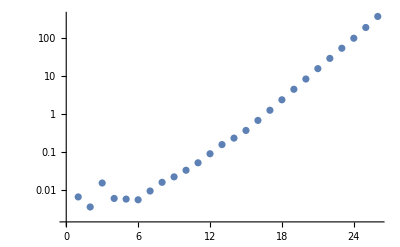

```mathematica
ListLogPlot[times]
```

```mathematica
(*ISU3L25=tmp;
Save[NotebookDirectory[]<>"index.m",{ISU3L25,index}];*)
```

```mathematica
(*Load[NotebookDirectory[]<>"index.m"];
tmp=ISU3L25;*)
```

#### Without Simplify

```mathematica
NN=3;
LL=30;
Timing[tmp=Sum[index[NN,L],{L,0,LL}]][[1]]
```

396.912

#### Analysis

```mathematica
tmp/.ξ->1
```

1+3 t^2+4 t^4+7 t^6+6 t^8+12 t^10+8 t^12+15 t^14+13 t^16+18 t^18+12 t^20+28 t^22+14 t^24+O[t]^26

```mathematica
tmp/.ξ->ⅈ
```

1-t^2+4 t^4-t^6+6 t^8-4 t^10+8 t^12-t^14+13 t^16-6 t^18+12 t^20-4 t^22+14 t^24+O[t]^26

```mathematica
coefs=Total[Abs[CoefficientList[If[#=!=0,ξ^Exponent[#,ξ]*#,0],ξ]]]&/@Expand[CoefficientList[tmp,t]];
coefs.Table[t^n,{n,0,Length[coefs]-1}]
```

1+3 t^2+4 t^3+4 t^4+8 t^5+11 t^6+16 t^7+22 t^8+32 t^9+40 t^10+64 t^11+88 t^12+120 t^13+163 t^14+228 t^15+309 t^16+420 t^17+562 t^18+748 t^19+992 t^20+1312 t^21+1712 t^22+2256 t^23+2934 t^24+3808 t^25

```mathematica
coefs=Max[Table[Abs[#/.ξ->N[Exp[2π ⅈ n/1000],10]],{n,1,1000}]]&/@Expand[CoefficientList[tmp,t]]
```

{1,0,3.,3.07920075,4.,5.9489018,10.149181,9.38045,18.359707,24.597272,28.,49.756374,70.176866,86.669988,130.77542,178.29695,235.55924,329.79527,444.5547,578.71734,783.51952,1030.6788,1342.2813,1775.6366,2308.2967,2982.2442}

### flavored MacDonald index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_,b_,s_]:=1-((1-b s x)(1-b^-1 s x))/(1-x^2)

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j,b^j,s^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=20;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify][[1]]
```

21.6443

```mathematica
Total[Abs[Flatten[CoefficientList[If[#===0,1,b^Exponent[#,b]]#,{b,s}]]]]&/@CoefficientList[tmp,x]
```

{1,0,3,4,4,8,11,16,26,32,44,68,100,128,187,252,353,468,642,844,1124}

```mathematica
Total[Abs[Flatten[CoefficientList[If[#===0,1,b^Exponent[#,b]]#,{b,s}]]]]&/@CoefficientList[tmp2,x]
```

{1,0,3,4,4,8,11,16,22,32,40,64,88,120,163,228,309,420,562,748,992}

```mathematica
NN=2;
LL=32;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify];
```

$Aborted

### flavored Hall-Littlewood index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_,b_]:=1-(1-b x)(1-b^-1 x)

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j,b^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=18;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify]
```

{7.2715,1+(1+1/b^2+b^2) x^2+(1/b^3+b^3) x^3+(1+1/b^4+b^4) x^4+(1/b^5+1/b^3+b^3+b^5) x^5+(1+2/b^6+2 b^6) x^6+(1/b^7+1/b^3+b^3+b^7) x^7+(1+2/b^8+1/b^6+b^6+2 b^8) x^8+(2/b^9+1/b^3+b^3+2 b^9) x^9+(1+2/b^10+1/b^6+b^6+2 b^10) x^10+((2+b^2+b^8+b^14+b^20+2 b^22) x^11)/b^11+(1+3/b^12+1/b^6+b^6+3 b^12) x^12+(2/b^13+1/b^9+1/b^3+b^3+b^9+2 b^13) x^13+(1+3/b^14+1/b^12+1/b^6+b^6+b^12+3 b^14) x^14+(3/b^15+1/b^9+1/b^3+b^3+b^9+3 b^15) x^15+(1+3/b^16+1/b^12+1/b^6+b^6+b^12+3 b^16) x^16+((3+b^2+b^8+b^14+b^20+b^26+b^32+3 b^34) x^17)/b^17+(1+4/b^18+1/b^12+1/b^6+b^6+b^12+4 b^18) x^18+O[x]^19}

### TODO: faster flavored Schur index

```mathematica
indexNumξ[LL_,L_,ξ_]:=indexNumξ[LL,L,ξ]=Module[{as},
as=aVectors[L];
Sum[Product[Series[f[t^j,ξ^j],{t,0,LL}]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=30;
Chop[Series[Sum[indexNumξ[LL,L,-1],{L,0,LL}],{t,0,LL}]]
```

## GAP

### Analysis

```mathematica
(*Do[
level=Switch[type,
"16",50,
"us",50,
"fs",35,
"um",35,
"fm",30,
"sx",30
];
file=NotebookDirectory[]<>"indU/"<>type<>"_"<>ToString[NN]<>"_"<>ToString[level]<>".m";
indexGAP[type,NN];
DeleteFile[file];
Save[file,f]
,
{type,{"16","us","fs","um","fm"}}
,
{NN,1,10}
]*)
```

```mathematica
Clear[indexGAP,indexX]
indexGAP[type_,N_,level_]:=Module[{file},
file=NotebookDirectory[]<>"ind/"<>type<>"_"<>ToString[N]<>"_"<>ToString[level]<>".mx";
Get[file];
f
];
indexGAP[type_,N_]:=Module[{level},
level=Switch[type,
"16",50,
"us",50,
"fs",35,
"um",35,
"fm",30,
"sx",30
];
indexGAP[type,N,level]
];
```

```mathematica
(* fixing some failure to simplify *)
Simp[type_,N_]:=Module[{file,level,cl},
level=Switch[type,
"16",50,
"us",50,
"fs",35,
"um",35,
"fm",30
];
file=NotebookDirectory[]<>"ind/"<>type<>"_"<>ToString[N]<>"_"<>ToString[level]<>".mx";
Get[file];
cl=Expand[CoefficientList[f,x]];
f=Sum[Normal[Simplify[Series[cl[[n+1]],{b,0,n}]]]x^n,{n,0,level}]+O[x]^(level+1);
DumpSave[file,f];
(*(If[#=!=0,Normal[Simplify[Series[#,{b,0,Exponent[#,b]}]]],0]&/@Expand[CoefficientList[f,x]]).Table[x^n,{n,0,level}]+O[x]^(level+1)*)
];
```

```mathematica
(*Monitor[
Do[
Simp[type,NN]
,
{type,{"fs","fm"}}
,
{NN,2,10}
]
,{type,NN}
]*)
```

```mathematica
indexX[type_,N_]:=indexX[type,N]=Module[{coefs,cl},
(*If[type=="16" || type=="us", Return[Normal[indexGAP[type,N]]]];*)
indexGAP[type,N];
cl=Expand[CoefficientList[f,x]];
coefs=Table[Total[Abs[CoefficientList[If[cl[[i]]=!=0,b^(i-1)*s^(3(i-1))cl[[i]],0],{b,s}]//Flatten]],{i,1,Length[cl]}];
(*coefs=Total[Abs[CoefficientList[If[#=!=0,b^Exponent[#,b]s^Exponent[#,s^-1]#,0],{b,s}]//Flatten]]&/@Expand[CoefficientList[f,x]];*)
coefs.Table[x^n,{n,0,Length[coefs]-1}]
];
```

```mathematica
file=NotebookDirectory[]<>"ind.mx";
Do[
	Print[type," ",NN];
	indexX[type,NN];
	DumpSave[file,indexX];
,
	{type,{"16","us","fs","fm","um","sx"}}
,
	{NN,2,10}
];
```

```mathematica
(*file=NotebookDirectory[]<>"indU.mx";
Do[
	Print[type," ",NN];
	indexX[type,NN];
	DumpSave[file,indexX];
,
	{type,{"16","us","fs","fm","um"}}
,
	{NN,1,10}
];*)
```

### Data SU(N)

```mathematica
Clear[indexX];
Get[NotebookDirectory[]<>"ind.mx"];
```

```mathematica
Table[CoefficientList[indexX["fm",NN],x],{NN,2,10,2}]//MatrixForm
Table[CoefficientList[indexX["fm",NN],x],{NN,3,10,2}]//MatrixForm
```

(1 | 0 | 3 | 4 | 9 | 12 | 22 | 36 | 60 | 88 | 135 | 204 | 302 | 432 | 627 | 900 | 1269 | 1764 | 2451 | 3384 | 4629 | 6268 | 8460 | 11376 | 15183 | 20124 | 26595 | 35008 | 45828 | 59700 | 77522
1 | 0 | 3 | 4 | 9 | 10 | 22 | 26 | 51 | 66 | 108 | 148 | 241 | 326 | 489 | 676 | 990 | 1358 | 1919 | 2614 | 3660 | 4958 | 6759 | 9080 | 12288 | 16354 | 21789 | 28770 | 38043 | 49842 | 65161
1 | 0 | 3 | 4 | 9 | 16 | 26 | 40 | 59 | 96 | 120 | 208 | 245 | 404 | 469 | 780 | 901 | 1436 | 1664 | 2600 | 3067 | 4620 | 5529 | 8124 | 9857 | 14040 | 17245 | 24152 | 29918 | 40920 | 51052
1 | 0 | 3 | 4 | 9 | 16 | 26 | 48 | 71 | 118 | 152 | 266 | 303 | 554 | 593 | 1068 | 1112 | 1974 | 2025 | 3496 | 3466 | 6034 | 5803 | 10162 | 9762 | 16840 | 16243 | 27478 | 27027 | 44432 | 44471
1 | 0 | 3 | 4 | 9 | 16 | 26 | 48 | 71 | 128 | 170 | 296 | 381 | 640 | 793 | 1308 | 1558 | 2504 | 2953 | 4608 | 5376 | 8132 | 9359 | 13956 | 15647 | 23276 | 25850 | 38012 | 41916 | 60848 | 66707)

(1 | 0 | 3 | 4 | 4 | 8 | 11 | 16 | 26 | 32 | 44 | 68 | 100 | 128 | 187 | 252 | 353 | 468 | 642 | 844 | 1124 | 1480 | 1936 | 2528 | 3298 | 4244 | 5460 | 7004 | 8928 | 11436 | 14475
1 | 0 | 3 | 4 | 9 | 16 | 19 | 36 | 46 | 64 | 85 | 116 | 159 | 180 | 257 | 308 | 417 | 488 | 669 | 796 | 1055 | 1276 | 1642 | 2012 | 2530 | 3132 | 3899 | 4844 | 5980 | 7356 | 9217
1 | 0 | 3 | 4 | 9 | 16 | 26 | 48 | 62 | 112 | 133 | 220 | 284 | 400 | 533 | 688 | 923 | 1124 | 1509 | 1792 | 2411 | 2800 | 3638 | 4392 | 5454 | 6668 | 8070 | 9796 | 11749 | 14248 | 16840
1 | 0 | 3 | 4 | 9 | 16 | 26 | 48 | 71 | 128 | 159 | 288 | 356 | 580 | 760 | 1104 | 1462 | 1984 | 2602 | 3400 | 4506 | 5648 | 7417 | 9136 | 11932 | 14544 | 18512 | 22640 | 28036 | 34708 | 41532)

```mathematica
Join[{Table[i,{i,0,30}]},Flatten[Table[{CoefficientList[indexX["us",NN],x][[1;;31]],CoefficientList[indexX["fs",NN],x][[1;;31]]},{NN,2,9,2}],1]]//Transpose//MatrixForm//TeXForm
```

\left(
\begin{array}{ccccccccc}
 0 & 1 & 1 & 1 & 1 & 1 & 1 & 1 & 1 \\
 1 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 2 & 3 & 3 & 3 & 3 & 3 & 3 & 3 & 3 \\
 3 & 4 & 4 & 0 & 4 & 0 & 4 & 0 & 4 \\
 4 & 9 & 9 & 9 & 9 & 9 & 9 & 9 & 9 \\
 5 & 12 & 12 & 6 & 10 & 0 & 8 & 0 & 8 \\
 6 & 22 & 22 & 22 & 22 & 22 & 22 & 22 & 22 \\
 7 & 36 & 36 & 18 & 26 & 8 & 20 & 0 & 16 \\
 8 & 60 & 60 & 51 & 51 & 51 & 51 & 51 & 51 \\
 9 & 88 & 88 & 54 & 66 & 24 & 48 & 10 & 38 \\
 10 & 135 & 135 & 108 & 108 & 108 & 108 & 108 & 108 \\
 11 & 204 & 204 & 132 & 148 & 72 & 108 & 30 & 78 \\
 12 & 302 & 302 & 241 & 241 & 221 & 221 & 221 & 221 \\
 13 & 432 & 432 & 306 & 326 & 176 & 228 & 90 & 166 \\
 14 & 627 & 627 & 489 & 489 & 429 & 429 & 429 & 429 \\
 15 & 900 & 900 & 648 & 676 & 408 & 488 & 220 & 340 \\
 16 & 1269 & 1269 & 990 & 990 & 845 & 845 & 810 & 810 \\
 17 & 1764 & 1764 & 1326 & 1358 & 864 & 972 & 510 & 686 \\
 18 & 2451 & 2451 & 1919 & 1919 & 1584 & 1584 & 1479 & 1479 \\
 19 & 3384 & 3384 & 2574 & 2614 & 1768 & 1912 & 1080 & 1336 \\
 20 & 4629 & 4629 & 3660 & 3660 & 2955 & 2955 & 2694 & 2694 \\
 21 & 6268 & 6268 & 4910 & 4958 & 3432 & 3628 & 2210 & 2574 \\
 22 & 8460 & 8460 & 6759 & 6759 & 5369 & 5369 & 4761 & 4761 \\
 23 & 11376 & 11376 & 9024 & 9080 & 6480 & 6732 & 4290 & 4806 \\
 24 & 15183 & 15183 & 12288 & 12288 & 9653 & 9653 & 8354 & 8354 \\
 25 & 20124 & 20124 & 16290 & 16354 & 11832 & 12152 & 8100 & 8812 \\
 26 & 26595 & 26595 & 21789 & 21789 & 16989 & 16989 & 14397 & 14397 \\
 27 & 35008 & 35008 & 28694 & 28770 & 21232 & 21640 & 14790 & 15750 \\
 28 & 45828 & 45828 & 38043 & 38043 & 29578 & 29578 & 24597 & 24597 \\
 29 & 59700 & 59700 & 49758 & 49842 & 37128 & 37632 & 26400 & 27668 \\
 30 & 77522 & 77522 & 65161 & 65161 & 50596 & 50596 & 41413 & 41413 \\
\end{array}
\right)

```mathematica
Join[{Table[i,{i,0,30}]},Flatten[Table[{CoefficientList[indexX["us",NN],x][[1;;31]],CoefficientList[indexX["fs",NN],x][[1;;31]]},{NN,3,10,2}],1]]//Transpose//MatrixForm//TeXForm
```

\left(
\begin{array}{ccccccccc}
 0 & 1 & 1 & 1 & 1 & 1 & 1 & 1 & 1 \\
 1 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 2 & 3 & 3 & 3 & 3 & 3 & 3 & 3 & 3 \\
 3 & 0 & 4 & 0 & 4 & 0 & 4 & 0 & 4 \\
 4 & 4 & 4 & 9 & 9 & 9 & 9 & 9 & 9 \\
 5 & 0 & 8 & 0 & 8 & 0 & 8 & 0 & 8 \\
 6 & 7 & 11 & 15 & 15 & 22 & 22 & 22 & 22 \\
 7 & 0 & 16 & 0 & 16 & 0 & 16 & 0 & 16 \\
 8 & 6 & 22 & 30 & 30 & 42 & 42 & 51 & 51 \\
 9 & 0 & 32 & 0 & 28 & 0 & 32 & 0 & 32 \\
 10 & 12 & 40 & 45 & 45 & 81 & 81 & 97 & 97 \\
 11 & 0 & 64 & 0 & 52 & 0 & 60 & 0 & 64 \\
 12 & 8 & 88 & 67 & 79 & 140 & 140 & 188 & 188 \\
 13 & 0 & 120 & 0 & 88 & 0 & 112 & 0 & 120 \\
 14 & 15 & 163 & 99 & 143 & 231 & 231 & 330 & 330 \\
 15 & 0 & 228 & 0 & 160 & 0 & 192 & 0 & 224 \\
 16 & 13 & 309 & 135 & 243 & 351 & 351 & 568 & 568 \\
 17 & 0 & 420 & 0 & 272 & 0 & 328 & 0 & 388 \\
 18 & 18 & 562 & 175 & 407 & 551 & 563 & 918 & 918 \\
 19 & 0 & 748 & 0 & 480 & 0 & 528 & 0 & 664 \\
 20 & 12 & 992 & 231 & 679 & 783 & 815 & 1452 & 1452 \\
 21 & 0 & 1312 & 0 & 800 & 0 & 840 & 0 & 1104 \\
 22 & 28 & 1712 & 306 & 1114 & 1134 & 1286 & 2233 & 2233 \\
 23 & 0 & 2256 & 0 & 1356 & 0 & 1304 & 0 & 1728 \\
 24 & 14 & 2934 & 354 & 1818 & 1546 & 1934 & 3344 & 3344 \\
 25 & 0 & 3808 & 0 & 2224 & 0 & 2012 & 0 & 2720 \\
 26 & 24 & 4900 & 465 & 2961 & 2142 & 2958 & 4884 & 4884 \\
 27 & 0 & 6308 & 0 & 3652 & 0 & 3080 & 0 & 4144 \\
 28 & 24 & 8068 & 540 & 4764 & 2835 & 4431 & 7004 & 7212 \\
 29 & 0 & 10312 & 0 & 5872 & 0 & 4804 & 0 & 6220 \\
 30 & 31 & 13107 & 681 & 7597 & 3758 & 6526 & 9856 & 10420 \\
\end{array}
\right)

```mathematica
Table[CoefficientList[indexX["fs",NN],x],{NN,2,10,2}]//MatrixForm
Table[CoefficientList[indexX["fs",NN],x],{NN,3,10,2}]//MatrixForm
```

(1 | 0 | 3 | 4 | 9 | 12 | 22 | 36 | 60 | 88 | 135 | 204 | 302 | 432 | 627 | 900 | 1269 | 1764 | 2451 | 3384 | 4629 | 6268 | 8460 | 11376 | 15183 | 20124 | 26595 | 35008 | 45828 | 59700 | 77522 | 100332 | 129309 | 165988 | 212463 | 271164
1 | 0 | 3 | 4 | 9 | 10 | 22 | 26 | 51 | 66 | 108 | 148 | 241 | 326 | 489 | 676 | 990 | 1358 | 1919 | 2614 | 3660 | 4958 | 6759 | 9080 | 12288 | 16354 | 21789 | 28770 | 38043 | 49842 | 65161 | 84750 | 110127 | 142216 | 183177 | 235056
1 | 0 | 3 | 4 | 9 | 8 | 22 | 20 | 51 | 48 | 108 | 108 | 221 | 228 | 429 | 488 | 845 | 972 | 1584 | 1912 | 2955 | 3628 | 5369 | 6732 | 9653 | 12152 | 16989 | 21640 | 29578 | 37632 | 50596 | 64568 | 85572 | 108892 | 142647 | 181364
1 | 0 | 3 | 4 | 9 | 8 | 22 | 16 | 51 | 38 | 108 | 78 | 221 | 166 | 429 | 340 | 810 | 686 | 1479 | 1336 | 2694 | 2574 | 4761 | 4806 | 8354 | 8812 | 14397 | 15750 | 24597 | 27668 | 41413 | 47662 | 69156 | 81038 | 114048 | 135472
1 | 0 | 3 | 4 | 9 | 8 | 22 | 16 | 51 | 32 | 108 | 64 | 221 | 128 | 429 | 256 | 810 | 516 | 1479 | 1008 | 2640 | 1904 | 4599 | 3552 | 7945 | 6440 | 13440 | 11556 | 22536 | 20332 | 37275 | 35280 | 61149 | 60084 | 99198 | 100916)

(1 | 0 | 3 | 4 | 4 | 8 | 11 | 16 | 22 | 32 | 40 | 64 | 88 | 120 | 163 | 228 | 309 | 420 | 562 | 748 | 992 | 1312 | 1712 | 2256 | 2934 | 3808 | 4900 | 6308 | 8068 | 10312 | 13107 | 16612 | 20982 | 26432 | 33179 | 41556
1 | 0 | 3 | 4 | 9 | 8 | 15 | 16 | 30 | 28 | 45 | 52 | 79 | 88 | 143 | 160 | 243 | 272 | 407 | 480 | 679 | 800 | 1114 | 1356 | 1818 | 2224 | 2961 | 3652 | 4764 | 5872 | 7597 | 9412 | 12021 | 14864 | 18817 | 23284
1 | 0 | 3 | 4 | 9 | 8 | 22 | 16 | 42 | 32 | 81 | 60 | 140 | 112 | 231 | 192 | 351 | 328 | 563 | 528 | 815 | 840 | 1286 | 1304 | 1934 | 2012 | 2958 | 3080 | 4431 | 4804 | 6526 | 7272 | 9574 | 11056 | 14077 | 16616
1 | 0 | 3 | 4 | 9 | 8 | 22 | 16 | 51 | 32 | 97 | 64 | 188 | 120 | 330 | 224 | 568 | 388 | 918 | 664 | 1452 | 1104 | 2233 | 1728 | 3344 | 2720 | 4884 | 4144 | 7212 | 6220 | 10420 | 9092 | 15089 | 13400 | 21831 | 19416)

```mathematica
Table[CoefficientList[indexX["us",NN],x],{NN,2,10,2}]//MatrixForm
Table[CoefficientList[indexX["us",NN],x],{NN,3,10,2}]//MatrixForm
```

(1 | 0 | 3 | 4 | 9 | 12 | 22 | 36 | 60 | 88 | 135 | 204 | 302 | 432 | 627 | 900 | 1269 | 1764 | 2451 | 3384 | 4629 | 6268 | 8460 | 11376 | 15183 | 20124 | 26595 | 35008 | 45828 | 59700 | 77522 | 100332 | 129309 | 165988 | 212463 | 271164 | 344881 | 437220 | 552864 | 697288 | 876897 | 1099776 | 1376109 | 1717920 | 2139381 | 2657968 | 3295386 | 4077348 | 5034052 | 6202440 | 7627740
1 | 0 | 3 | 0 | 9 | 6 | 22 | 18 | 51 | 54 | 108 | 132 | 241 | 306 | 489 | 648 | 990 | 1326 | 1919 | 2574 | 3660 | 4910 | 6759 | 9024 | 12288 | 16290 | 21789 | 28694 | 38043 | 49758 | 65161 | 84654 | 110127 | 142108 | 183177 | 234936 | 301074 | 383832 | 488400 | 619242 | 783864 | 988614 | 1244156 | 1561410 | 1956105 | 2443490 | 3045906 | 3788214 | 4702892 | 5824674 | 7200099
1 | 0 | 3 | 0 | 9 | 0 | 22 | 8 | 51 | 24 | 108 | 72 | 221 | 176 | 429 | 408 | 845 | 864 | 1584 | 1768 | 2955 | 3432 | 5369 | 6480 | 9653 | 11832 | 16989 | 21232 | 29578 | 37128 | 50596 | 63952 | 85572 | 108136 | 142647 | 180456 | 235169 | 296744 | 382875 | 482528 | 617323 | 775104 | 984393 | 1232872 | 1555611 | 1940928 | 2435024 | 3028872 | 3780226 | 4684656 | 5819226
1 | 0 | 3 | 0 | 9 | 0 | 22 | 0 | 51 | 10 | 108 | 30 | 221 | 90 | 429 | 220 | 810 | 510 | 1479 | 1080 | 2694 | 2210 | 4761 | 4290 | 8354 | 8100 | 14397 | 14790 | 24597 | 26400 | 41413 | 45990 | 69156 | 78890 | 114048 | 132720 | 186509 | 220320 | 301776 | 360430 | 484209 | 582930 | 769542 | 931500 | 1213332 | 1474100 | 1896507 | 2309190 | 2942644 | 3586590 | 4529958
1 | 0 | 3 | 0 | 9 | 0 | 22 | 0 | 51 | 0 | 108 | 12 | 221 | 36 | 429 | 108 | 810 | 264 | 1479 | 612 | 2640 | 1296 | 4599 | 2652 | 7945 | 5148 | 13440 | 9720 | 22536 | 17748 | 37275 | 31680 | 61149 | 55188 | 99198 | 94416 | 159786 | 158508 | 254943 | 262468 | 404019 | 428028 | 635079 | 689832 | 991740 | 1098328 | 1537344 | 1731180 | 2368298 | 2700936 | 3623697)

(1 | 0 | 3 | 0 | 4 | 0 | 7 | 0 | 6 | 0 | 12 | 0 | 8 | 0 | 15 | 0 | 13 | 0 | 18 | 0 | 12 | 0 | 28 | 0 | 14 | 0 | 24 | 0 | 24 | 0 | 31 | 0 | 18 | 0 | 39 | 0 | 20 | 0 | 42 | 0 | 32 | 0 | 36 | 0 | 24 | 0 | 60 | 0 | 31 | 0 | 42
1 | 0 | 3 | 0 | 9 | 0 | 15 | 0 | 30 | 0 | 45 | 0 | 67 | 0 | 99 | 0 | 135 | 0 | 175 | 0 | 231 | 0 | 306 | 0 | 354 | 0 | 465 | 0 | 540 | 0 | 681 | 0 | 765 | 0 | 945 | 0 | 1040 | 0 | 1305 | 0 | 1386 | 0 | 1695 | 0 | 1779 | 0 | 2205 | 0 | 2290 | 0 | 2754
1 | 0 | 3 | 0 | 9 | 0 | 22 | 0 | 42 | 0 | 81 | 0 | 140 | 0 | 231 | 0 | 351 | 0 | 551 | 0 | 783 | 0 | 1134 | 0 | 1546 | 0 | 2142 | 0 | 2835 | 0 | 3758 | 0 | 4818 | 0 | 6237 | 0 | 7826 | 0 | 9885 | 0 | 12159 | 0 | 14974 | 0 | 18261 | 0 | 22113 | 0 | 26511 | 0 | 31668
1 | 0 | 3 | 0 | 9 | 0 | 22 | 0 | 51 | 0 | 97 | 0 | 188 | 0 | 330 | 0 | 568 | 0 | 918 | 0 | 1452 | 0 | 2233 | 0 | 3344 | 0 | 4884 | 0 | 7004 | 0 | 9856 | 0 | 13653 | 0 | 18699 | 0 | 25080 | 0 | 33462 | 0 | 43918 | 0 | 57304 | 0 | 73668 | 0 | 94482 | 0 | 119262 | 0 | 150285)

```mathematica
Table[CoefficientList[indexX["um",NN],x],{NN,2,10,2}]//MatrixForm
Table[CoefficientList[indexX["um",NN],x],{NN,3,10,2}]//MatrixForm
```

(1 | 0 | 3 | 4 | 9 | 12 | 22 | 36 | 60 | 88 | 135 | 204 | 302 | 432 | 627 | 900 | 1269 | 1764 | 2451 | 3384 | 4629 | 6268 | 8460 | 11376 | 15183 | 20124 | 26595 | 35008 | 45828 | 59700 | 77522 | 100332 | 129309 | 165988 | 212463 | 271164
1 | 0 | 3 | 4 | 9 | 10 | 22 | 26 | 51 | 66 | 108 | 148 | 241 | 326 | 489 | 676 | 990 | 1358 | 1919 | 2614 | 3660 | 4958 | 6759 | 9080 | 12288 | 16354 | 21789 | 28770 | 38043 | 49842 | 65161 | 84750 | 110127 | 142216 | 183177 | 235056
1 | 0 | 3 | 4 | 9 | 16 | 24 | 40 | 53 | 96 | 108 | 208 | 221 | 404 | 429 | 780 | 845 | 1436 | 1584 | 2600 | 2955 | 4620 | 5369 | 8124 | 9653 | 14040 | 16989 | 24152 | 29578 | 40920 | 50596 | 68780 | 85572 | 114220 | 142647 | 188024
1 | 0 | 3 | 4 | 9 | 16 | 24 | 48 | 67 | 118 | 146 | 266 | 303 | 554 | 585 | 1068 | 1112 | 1974 | 2021 | 3496 | 3450 | 6034 | 5783 | 10154 | 9712 | 16828 | 16155 | 27458 | 26845 | 44384 | 44219 | 71030 | 72590 | 113134 | 118218 | 178836
1 | 0 | 3 | 4 | 9 | 16 | 24 | 48 | 67 | 128 | 164 | 296 | 381 | 640 | 793 | 1308 | 1558 | 2504 | 2953 | 4604 | 5368 | 8132 | 9331 | 13940 | 15571 | 23240 | 25650 | 37944 | 41732 | 60708 | 66575 | 95688 | 104527 | 148744 | 162200 | 228744)

(1 | 0 | 3 | 4 | 4 | 8 | 7 | 16 | 18 | 20 | 20 | 32 | 44 | 48 | 75 | 68 | 105 | 100 | 174 | 168 | 264 | 284 | 382 | 444 | 556 | 652 | 772 | 912 | 1124 | 1400 | 1611 | 2076 | 2288 | 3020 | 3301 | 4308
1 | 0 | 3 | 4 | 9 | 16 | 17 | 36 | 40 | 64 | 83 | 104 | 147 | 160 | 233 | 232 | 375 | 364 | 529 | 592 | 763 | 944 | 1044 | 1404 | 1508 | 2056 | 2133 | 2952 | 3180 | 4164 | 4715 | 5868 | 6787 | 8116 | 9529 | 11888
1 | 0 | 3 | 4 | 9 | 16 | 24 | 48 | 58 | 112 | 127 | 220 | 284 | 400 | 525 | 684 | 911 | 1104 | 1471 | 1712 | 2371 | 2712 | 3474 | 4172 | 5180 | 6352 | 7298 | 8996 | 10299 | 13036 | 14240 | 18964 | 20368 | 26112 | 28589 | 34992
1 | 0 | 3 | 4 | 9 | 16 | 24 | 48 | 67 | 128 | 153 | 288 | 356 | 580 | 760 | 1104 | 1450 | 1980 | 2572 | 3376 | 4442 | 5560 | 7347 | 9036 | 11820 | 14300 | 18240 | 22052 | 27256 | 34000 | 40260 | 49656 | 57311 | 70720 | 80255 | 100096)

### Data U(N)

```mathematica
Clear[indexX];
Get[NotebookDirectory[]<>"indU.mx"];
```

```mathematica
Join[{Table[i,{i,0,30}]},Flatten[Table[{CoefficientList[indexX["fm",NN],x][[1;;31]]},{NN,2,9,1}],1]]//Transpose//MatrixForm//TeXForm
```

\left(
\begin{array}{ccccccccc}
 0 & 1 & 1 & 1 & 1 & 1 & 1 & 1 & 1 \\
 1 & 2 & 2 & 2 & 2 & 2 & 2 & 2 & 2 \\
 2 & 6 & 6 & 6 & 6 & 6 & 6 & 6 & 6 \\
 3 & 8 & 12 & 12 & 12 & 12 & 12 & 12 & 12 \\
 4 & 12 & 21 & 26 & 26 & 26 & 26 & 26 & 26 \\
 5 & 16 & 30 & 42 & 48 & 48 & 48 & 48 & 48 \\
 6 & 24 & 42 & 68 & 83 & 90 & 90 & 90 & 90 \\
 7 & 24 & 60 & 96 & 130 & 148 & 156 & 156 & 156 \\
 8 & 31 & 82 & 142 & 198 & 240 & 261 & 270 & 270 \\
 9 & 40 & 102 & 186 & 290 & 362 & 412 & 436 & 446 \\
 10 & 48 & 124 & 260 & 410 & 548 & 636 & 694 & 721 \\
 11 & 52 & 164 & 332 & 564 & 780 & 952 & 1056 & 1122 \\
 12 & 68 & 204 & 426 & 766 & 1112 & 1390 & 1596 & 1716 \\
 13 & 64 & 238 & 536 & 1020 & 1524 & 1984 & 2324 & 2564 \\
 14 & 82 & 296 & 690 & 1319 & 2086 & 2786 & 3360 & 3762 \\
 15 & 96 & 340 & 832 & 1704 & 2780 & 3836 & 4732 & 5420 \\
 16 & 96 & 376 & 1040 & 2170 & 3667 & 5218 & 6608 & 7700 \\
 17 & 118 & 448 & 1236 & 2720 & 4754 & 7002 & 9044 & 10768 \\
 18 & 142 & 524 & 1470 & 3396 & 6150 & 9244 & 12294 & 14882 \\
 19 & 124 & 588 & 1736 & 4176 & 7796 & 12108 & 16440 & 20310 \\
 20 & 172 & 686 & 2058 & 5022 & 9874 & 15702 & 21800 & 27428 \\
 21 & 176 & 784 & 2398 & 6020 & 12296 & 20136 & 28572 & 36668 \\
 22 & 188 & 830 & 2862 & 7204 & 15176 & 25630 & 37210 & 48523 \\
 23 & 220 & 968 & 3304 & 8506 & 18424 & 32328 & 47888 & 63686 \\
 24 & 227 & 1096 & 3826 & 10157 & 22246 & 40342 & 61328 & 82914 \\
 25 & 256 & 1194 & 4310 & 12024 & 26696 & 49886 & 77746 & 107078 \\
 26 & 288 & 1398 & 4964 & 14120 & 31964 & 61042 & 97902 & 137332 \\
 27 & 304 & 1552 & 5588 & 16500 & 38248 & 73932 & 122148 & 174884 \\
 28 & 350 & 1621 & 6318 & 18926 & 45666 & 89160 & 151348 & 221106 \\
 29 & 320 & 1864 & 7144 & 21776 & 54080 & 107152 & 185784 & 277668 \\
 30 & 430 & 2044 & 8168 & 25122 & 63840 & 128784 & 226454 & 346300 \\
\end{array}
\right)

```mathematica
Table[CoefficientList[indexX["sx",NN],x],{NN,2,10,2}]//MatrixForm
Table[CoefficientList[indexX["sx",NN],x],{NN,1,10,2}]//MatrixForm
```

(1 | 4 | 12 | 16 | 32 | 60 | 60 | 198 | 159 | 562 | 560 | 1516 | 1806 | 4058 | 5344 | 10400 | 14246 | 26140 | 35620 | 61324 | 83886 | 142988 | 193658 | 321342 | 426389 | 689606 | 904270 | 1427764 | 1855468 | 2856610 | 3796488
1 | 4 | 12 | 32 | 74 | 124 | 138 | 342 | 768 | 880 | 1890 | 6158 | 7660 | 14204 | 50992 | 44498 | 159862 | 413558 | 338290 | 1721610 | 2350266 | 4849646 | 13872340 | 12688744 | 53834822 | 58933124 | 166982106 | 343912602 | 473866904 | 1423280906 | 1469874534
1 | 4 | 12 | 32 | 74 | 160 | 328 | 576 | 808 | 790 | 2154 | 4822 | 7442 | 7468 | 29228 | 83660 | 127949 | 125616 | 655838 | 1580460 | 1168024 | 5081746 | 16633006 | 18997112 | 42403600 | 165915986 | 213877482 | 408720154 | 1638235098 | 1974306336 | 4446326578
1 | 4 | 12 | 32 | 74 | 160 | 328 | 640 | 1204 | 2096 | 3244 | 4160 | 4064 | 9880 | 22690 | 39284 | 41656 | 82864 | 298962 | 760594 | 1265846 | 1001766 | 4143428 | 14515994 | 27911324 | 18497702 | 90210148 | 323928224 | 570889824 | 385959414 | 2545711954
1 | 4 | 12 | 32 | 74 | 160 | 328 | 640 | 1204 | 2196 | 3896 | 6608 | 10492 | 15072 | 18208 | 17420 | 40416 | 89920 | 162684 | 219512 | 214516 | 736832 | 2306442 | 5380530 | 9207839 | 8710648 | 18953774 | 79177146 | 208341790 | 347304474 | 218047278)

(1 | 4 | 5 | 10 | 8 | 16 | 19 | 28 | 30 | 40 | 48 | 74 | 71 | 102 | 120 | 164 | 172 | 238 | 264 | 360 | 383 | 496 | 554 | 724 | 782 | 1004 | 1108 | 1406 | 1522 | 1910 | 2103
1 | 4 | 12 | 32 | 49 | 68 | 182 | 272 | 376 | 1302 | 1262 | 3560 | 8264 | 8580 | 33658 | 27994 | 109264 | 150534 | 319364 | 657556 | 905738 | 2346776 | 2661978 | 7476892 | 8385176 | 22256720 | 26548816 | 64068806 | 82244495 | 178589316 | 243268390
1 | 4 | 12 | 32 | 74 | 160 | 279 | 348 | 512 | 1422 | 2580 | 2336 | 7912 | 24108 | 34315 | 45580 | 207130 | 357318 | 381062 | 1963568 | 3326326 | 4146136 | 19177784 | 25432026 | 51064577 | 177601690 | 137859738 | 618551086 | 1387432402 | 1450249632 | 6391596388
1 | 4 | 12 | 32 | 74 | 160 | 328 | 640 | 1123 | 1680 | 1904 | 2804 | 7416 | 14550 | 18846 | 25146 | 97020 | 262156 | 422304 | 345382 | 1754580 | 5236738 | 7473256 | 8569134 | 46729350 | 108080488 | 74567640 | 359926318 | 1192737174 | 1496000392 | 2732616644
1 | 4 | 12 | 32 | 74 | 160 | 328 | 640 | 1204 | 2196 | 3775 | 5948 | 8192 | 8720 | 12810 | 31358 | 63280 | 96812 | 85170 | 254780 | 853472 | 2073948 | 3518777 | 2958714 | 9088592 | 35487428 | 82083438 | 102998144 | 127210272 | 689496824 | 1831629760)

```mathematica
Table[CoefficientList[indexX["fm",NN],x],{NN,2,10,2}]//MatrixForm
Table[CoefficientList[indexX["fm",NN],x],{NN,1,10,2}]//MatrixForm
```

(1 | 2 | 6 | 8 | 12 | 16 | 24 | 24 | 31 | 40 | 48 | 52 | 68 | 64 | 82 | 96 | 96 | 118 | 142 | 124 | 172 | 176 | 188 | 220 | 227 | 256 | 288 | 304 | 350 | 320 | 430
1 | 2 | 6 | 12 | 26 | 42 | 68 | 96 | 142 | 186 | 260 | 332 | 426 | 536 | 690 | 832 | 1040 | 1236 | 1470 | 1736 | 2058 | 2398 | 2862 | 3304 | 3826 | 4310 | 4964 | 5588 | 6318 | 7144 | 8168
1 | 2 | 6 | 12 | 26 | 48 | 90 | 148 | 240 | 362 | 548 | 780 | 1112 | 1524 | 2086 | 2780 | 3667 | 4754 | 6150 | 7796 | 9874 | 12296 | 15176 | 18424 | 22246 | 26696 | 31964 | 38248 | 45666 | 54080 | 63840
1 | 2 | 6 | 12 | 26 | 48 | 90 | 156 | 270 | 436 | 694 | 1056 | 1596 | 2324 | 3360 | 4732 | 6608 | 9044 | 12294 | 16440 | 21800 | 28572 | 37210 | 47888 | 61328 | 77746 | 97902 | 122148 | 151348 | 185784 | 226454
1 | 2 | 6 | 12 | 26 | 48 | 90 | 156 | 270 | 446 | 732 | 1152 | 1790 | 2700 | 4036 | 5884 | 8502 | 12056 | 16940 | 23444 | 32184 | 43612 | 58682 | 78124 | 103241 | 135248 | 176100 | 227404 | 292068 | 372432 | 472240)

(1 | 2 | 3 | 2 | 4 | 4 | 3 | 6 | 4 | 6 | 8 | 6 | 9 | 6 | 12 | 10 | 12 | 16 | 8 | 20 | 13 | 20 | 20 | 20 | 28 | 22 | 32 | 22 | 36 | 26 | 43
1 | 2 | 6 | 12 | 21 | 30 | 42 | 60 | 82 | 102 | 124 | 164 | 204 | 238 | 296 | 340 | 376 | 448 | 524 | 588 | 686 | 784 | 830 | 968 | 1096 | 1194 | 1398 | 1552 | 1621 | 1864 | 2044
1 | 2 | 6 | 12 | 26 | 48 | 83 | 130 | 198 | 290 | 410 | 564 | 766 | 1020 | 1319 | 1704 | 2170 | 2720 | 3396 | 4176 | 5022 | 6020 | 7204 | 8506 | 10157 | 12024 | 14120 | 16500 | 18926 | 21776 | 25122
1 | 2 | 6 | 12 | 26 | 48 | 90 | 156 | 261 | 412 | 636 | 952 | 1390 | 1984 | 2786 | 3836 | 5218 | 7002 | 9244 | 12108 | 15702 | 20136 | 25630 | 32328 | 40342 | 49886 | 61042 | 73932 | 89160 | 107152 | 128784
1 | 2 | 6 | 12 | 26 | 48 | 90 | 156 | 270 | 446 | 721 | 1122 | 1716 | 2564 | 3762 | 5420 | 7700 | 10768 | 14882 | 20310 | 27428 | 36668 | 48523 | 63686 | 82914 | 107078 | 137332 | 174884 | 221106 | 277668 | 346300)

```mathematica
Join[{Table[i,{i,0,30}]},Table[CoefficientList[indexX["us",NN],x][[1;;31]],{NN,1,3,1}],Table[CoefficientList[indexX["fs",NN],x][[1;;31]],{NN,3,3,1}],Table[CoefficientList[indexX["us",NN],x][[1;;31]],{NN,4,9,1}]]//Transpose//MatrixForm//TeXForm
```

\left(
\begin{array}{ccccccccccc}
 0 & 1 & 1 & 1 & 1 & 1 & 1 & 1 & 1 & 1 & 1 \\
 1 & 2 & 2 & 2 & 2 & 2 & 2 & 2 & 2 & 2 & 2 \\
 2 & 1 & 4 & 4 & 4 & 4 & 4 & 4 & 4 & 4 & 4 \\
 3 & 2 & 4 & 8 & 8 & 8 & 8 & 8 & 8 & 8 & 8 \\
 4 & 2 & 6 & 9 & 9 & 14 & 14 & 14 & 14 & 14 & 14 \\
 5 & 0 & 8 & 14 & 14 & 18 & 24 & 24 & 24 & 24 & 24 \\
 6 & 3 & 8 & 20 & 20 & 28 & 33 & 40 & 40 & 40 & 40 \\
 7 & 2 & 8 & 24 & 24 & 40 & 50 & 56 & 64 & 64 & 64 \\
 8 & 0 & 13 & 30 & 30 & 52 & 72 & 84 & 91 & 100 & 100 \\
 9 & 2 & 12 & 34 & 34 & 70 & 98 & 122 & 136 & 144 & 154 \\
 10 & 2 & 12 & 46 & 46 & 88 & 134 & 168 & 196 & 212 & 221 \\
 11 & 2 & 16 & 52 & 52 & 104 & 176 & 232 & 272 & 304 & 322 \\
 12 & 1 & 14 & 60 & 60 & 140 & 224 & 312 & 378 & 424 & 460 \\
 13 & 2 & 16 & 70 & 70 & 168 & 280 & 408 & 512 & 588 & 640 \\
 14 & 0 & 24 & 76 & 76 & 196 & 367 & 528 & 680 & 800 & 886 \\
 15 & 2 & 16 & 88 & 88 & 240 & 448 & 672 & 896 & 1072 & 1208 \\
 16 & 4 & 18 & 102 & 102 & 278 & 546 & 865 & 1162 & 1422 & 1622 \\
 17 & 0 & 26 & 120 & 120 & 320 & 672 & 1078 & 1478 & 1864 & 2160 \\
 18 & 2 & 20 & 118 & 126 & 380 & 798 & 1336 & 1904 & 2408 & 2848 \\
 19 & 0 & 24 & 136 & 136 & 440 & 952 & 1648 & 2392 & 3080 & 3706 \\
 20 & 1 & 32 & 154 & 154 & 504 & 1136 & 2002 & 2976 & 3950 & 4784 \\
 21 & 4 & 24 & 160 & 160 & 562 & 1328 & 2424 & 3704 & 4972 & 6120 \\
 22 & 2 & 24 & 184 & 184 & 644 & 1554 & 2912 & 4544 & 6224 & 7809 \\
 23 & 0 & 32 & 200 & 200 & 720 & 1838 & 3472 & 5536 & 7760 & 9850 \\
 24 & 2 & 31 & 208 & 224 & 808 & 2079 & 4116 & 6730 & 9564 & 12348 \\
 25 & 2 & 28 & 234 & 234 & 910 & 2400 & 4872 & 8106 & 11742 & 15394 \\
 26 & 0 & 40 & 252 & 252 & 1000 & 2772 & 5744 & 9692 & 14344 & 19052 \\
 27 & 2 & 32 & 244 & 244 & 1120 & 3120 & 6648 & 11584 & 17384 & 23464 \\
 28 & 2 & 30 & 295 & 295 & 1240 & 3554 & 7752 & 13752 & 20968 & 28740 \\
 29 & 2 & 48 & 308 & 308 & 1360 & 4048 & 8976 & 16248 & 25204 & 35008 \\
 30 & 1 & 32 & 308 & 340 & 1488 & 4522 & 10304 & 19052 & 30112 & 42428 \\
\end{array}
\right)

```mathematica
Table[CoefficientList[indexX["fs",NN],x],{NN,2,10,2}]//MatrixForm
Table[CoefficientList[indexX["fs",NN],x],{NN,3,10,2}]//MatrixForm
```

(1 | 2 | 4 | 4 | 6 | 8 | 8 | 8 | 13 | 12 | 12 | 16 | 14 | 16 | 24 | 16 | 18 | 26 | 20 | 24 | 32 | 24 | 24 | 32 | 31 | 28 | 40 | 32 | 30 | 48 | 32 | 32 | 48 | 36 | 48 | 52
1 | 2 | 4 | 8 | 14 | 18 | 28 | 40 | 52 | 70 | 88 | 104 | 140 | 168 | 196 | 240 | 278 | 320 | 380 | 440 | 504 | 562 | 644 | 720 | 808 | 910 | 1000 | 1120 | 1240 | 1360 | 1488 | 1600 | 1789 | 1938 | 2100 | 2296
1 | 2 | 4 | 8 | 14 | 24 | 40 | 56 | 84 | 122 | 168 | 232 | 312 | 408 | 528 | 672 | 865 | 1078 | 1336 | 1648 | 2002 | 2424 | 2912 | 3472 | 4116 | 4872 | 5744 | 6648 | 7752 | 8976 | 10304 | 11872 | 13566 | 15424 | 17556 | 19896
1 | 2 | 4 | 8 | 14 | 24 | 40 | 64 | 100 | 144 | 212 | 304 | 424 | 588 | 800 | 1072 | 1422 | 1864 | 2408 | 3080 | 3950 | 4972 | 6224 | 7760 | 9564 | 11742 | 14344 | 17384 | 20968 | 25204 | 30112 | 35840 | 42548 | 50078 | 58888 | 69048
1 | 2 | 4 | 8 | 14 | 24 | 40 | 64 | 100 | 154 | 232 | 332 | 480 | 680 | 944 | 1304 | 1774 | 2384 | 3180 | 4200 | 5488 | 7120 | 9160 | 11680 | 14869 | 18740 | 23468 | 29280 | 36278 | 44720 | 54904 | 67040 | 81464 | 98658 | 118936 | 142792)

(1 | 2 | 4 | 8 | 9 | 14 | 20 | 24 | 30 | 34 | 46 | 52 | 60 | 70 | 76 | 88 | 102 | 120 | 126 | 136 | 154 | 160 | 184 | 200 | 224 | 234 | 252 | 244 | 295 | 308 | 340 | 360 | 374 | 396 | 420 | 444
1 | 2 | 4 | 8 | 14 | 24 | 33 | 50 | 72 | 98 | 134 | 176 | 224 | 280 | 367 | 448 | 546 | 672 | 798 | 952 | 1136 | 1328 | 1554 | 1838 | 2079 | 2400 | 2772 | 3120 | 3554 | 4048 | 4522 | 5082 | 5740 | 6342 | 7040 | 7824
1 | 2 | 4 | 8 | 14 | 24 | 40 | 64 | 91 | 136 | 196 | 272 | 378 | 512 | 680 | 896 | 1162 | 1478 | 1904 | 2392 | 2976 | 3704 | 4544 | 5536 | 6730 | 8106 | 9692 | 11584 | 13752 | 16248 | 19052 | 22312 | 25996 | 30182 | 34936 | 40240
1 | 2 | 4 | 8 | 14 | 24 | 40 | 64 | 100 | 154 | 221 | 322 | 460 | 640 | 886 | 1208 | 1622 | 2160 | 2848 | 3706 | 4784 | 6120 | 7809 | 9850 | 12348 | 15394 | 19052 | 23464 | 28740 | 35008 | 42428 | 51210 | 61524 | 73608 | 87760 | 104234)

```mathematica
Table[CoefficientList[indexX["us",NN],x],{NN,2,10,2}]//MatrixForm
Table[CoefficientList[indexX["us",NN],x],{NN,3,10,2}]//MatrixForm
```

(1 | 2 | 4 | 4 | 6 | 8 | 8 | 8 | 13 | 12 | 12 | 16 | 14 | 16 | 24 | 16 | 18 | 26 | 20 | 24 | 32 | 24 | 24 | 32 | 31 | 28 | 40 | 32 | 30 | 48 | 32 | 32 | 48 | 36 | 48 | 52 | 38 | 40 | 56 | 48 | 42 | 64 | 44 | 48 | 78 | 48 | 48 | 64 | 57 | 62 | 72
1 | 2 | 4 | 8 | 14 | 18 | 28 | 40 | 52 | 70 | 88 | 104 | 140 | 168 | 196 | 240 | 278 | 320 | 380 | 440 | 504 | 562 | 644 | 720 | 808 | 910 | 1000 | 1120 | 1240 | 1360 | 1488 | 1600 | 1789 | 1938 | 2100 | 2296 | 2452 | 2660 | 2880 | 3080 | 3292 | 3542 | 3784 | 4048 | 4400 | 4572 | 4868 | 5280 | 5502 | 5850 | 6280
1 | 2 | 4 | 8 | 14 | 24 | 40 | 56 | 84 | 122 | 168 | 232 | 312 | 408 | 528 | 672 | 865 | 1078 | 1336 | 1648 | 2002 | 2424 | 2912 | 3472 | 4116 | 4872 | 5744 | 6648 | 7752 | 8976 | 10304 | 11872 | 13566 | 15424 | 17556 | 19896 | 22414 | 25256 | 28336 | 31584 | 35462 | 39482 | 43728 | 48664 | 53820 | 59312 | 65584 | 72128 | 78972 | 86814 | 95004
1 | 2 | 4 | 8 | 14 | 24 | 40 | 64 | 100 | 144 | 212 | 304 | 424 | 588 | 800 | 1072 | 1422 | 1864 | 2408 | 3080 | 3950 | 4972 | 6224 | 7760 | 9564 | 11742 | 14344 | 17384 | 20968 | 25204 | 30112 | 35840 | 42548 | 50078 | 58888 | 69048 | 80474 | 93628 | 108608 | 125408 | 144536 | 166224 | 190348 | 217576 | 248200 | 282104 | 320064 | 362352 | 409356 | 461374 | 519180
1 | 2 | 4 | 8 | 14 | 24 | 40 | 64 | 100 | 154 | 232 | 332 | 480 | 680 | 944 | 1304 | 1774 | 2384 | 3180 | 4200 | 5488 | 7120 | 9160 | 11680 | 14869 | 18740 | 23468 | 29280 | 36278 | 44720 | 54904 | 67040 | 81464 | 98658 | 118936 | 142792 | 170902 | 203760 | 242120 | 286624 | 338366 | 398160 | 467148 | 546592 | 637680 | 742072 | 861336 | 997304 | 1151968 | 1327588 | 1526548)

(1 | 2 | 4 | 8 | 9 | 14 | 20 | 24 | 30 | 34 | 46 | 52 | 60 | 70 | 76 | 88 | 102 | 120 | 118 | 136 | 154 | 160 | 184 | 200 | 208 | 234 | 252 | 244 | 295 | 308 | 308 | 360 | 374 | 368 | 420 | 444 | 422 | 494 | 528 | 520 | 567 | 602 | 580 | 660 | 696 | 656 | 752 | 784 | 748 | 860 | 900
1 | 2 | 4 | 8 | 14 | 24 | 33 | 50 | 72 | 98 | 134 | 176 | 224 | 280 | 367 | 448 | 546 | 672 | 798 | 952 | 1136 | 1328 | 1554 | 1838 | 2079 | 2400 | 2772 | 3120 | 3554 | 4048 | 4522 | 5082 | 5740 | 6342 | 7040 | 7824 | 8668 | 9548 | 10556 | 11550 | 12638 | 13904 | 15114 | 16464 | 17952 | 19412 | 21036 | 22848 | 24640 | 26648 | 28644
1 | 2 | 4 | 8 | 14 | 24 | 40 | 64 | 91 | 136 | 196 | 272 | 378 | 512 | 680 | 896 | 1162 | 1478 | 1904 | 2392 | 2976 | 3704 | 4544 | 5536 | 6730 | 8106 | 9692 | 11584 | 13752 | 16248 | 19052 | 22312 | 25996 | 30182 | 34936 | 40240 | 46246 | 52976 | 60504 | 68904 | 78244 | 88592 | 100032 | 112640 | 126820 | 142132 | 159064 | 177776 | 198044 | 220386 | 244812
1 | 2 | 4 | 8 | 14 | 24 | 40 | 64 | 100 | 154 | 221 | 322 | 460 | 640 | 886 | 1208 | 1622 | 2160 | 2848 | 3706 | 4784 | 6120 | 7809 | 9850 | 12348 | 15394 | 19052 | 23464 | 28740 | 35008 | 42428 | 51210 | 61524 | 73608 | 87760 | 104234 | 123147 | 145234 | 170618 | 199680 | 233178 | 271344 | 314804 | 364408 | 420660 | 484170 | 556142 | 637258 | 728288 | 830794 | 945492)

```mathematica
Table[CoefficientList[indexX["um",NN],x],{NN,2,10,2}]//MatrixForm
Table[CoefficientList[indexX["um",NN],x],{NN,3,10,2}]//MatrixForm
```

(1 | 2 | 6 | 8 | 12 | 12 | 20 | 20 | 21 | 28 | 36 | 32 | 48 | 44 | 42 | 60 | 64 | 70 | 94 | 64 | 100 | 104 | 108 | 140 | 125 | 132 | 176 | 168 | 202 | 172 | 224 | 220 | 270 | 312 | 228 | 324
1 | 2 | 6 | 12 | 26 | 42 | 68 | 96 | 142 | 186 | 256 | 332 | 422 | 528 | 674 | 812 | 1008 | 1200 | 1386 | 1584 | 1862 | 2170 | 2582 | 3004 | 3466 | 3790 | 4224 | 4784 | 5240 | 6028 | 6918 | 7584 | 8185 | 9274 | 10104 | 10832
1 | 2 | 6 | 12 | 26 | 48 | 90 | 148 | 240 | 362 | 548 | 780 | 1112 | 1524 | 2086 | 2780 | 3667 | 4754 | 6150 | 7796 | 9874 | 12296 | 15176 | 18424 | 22126 | 26124 | 31030 | 37020 | 44386 | 52780 | 62576 | 73176 | 84748 | 97144 | 110622 | 125112
1 | 2 | 6 | 12 | 26 | 48 | 90 | 156 | 270 | 436 | 694 | 1056 | 1596 | 2324 | 3360 | 4732 | 6608 | 9044 | 12294 | 16440 | 21800 | 28572 | 37210 | 47888 | 61328 | 77746 | 97902 | 122148 | 151344 | 185780 | 226446 | 273552 | 328172 | 390962 | 463868 | 554764
1 | 2 | 6 | 12 | 26 | 48 | 90 | 156 | 270 | 446 | 732 | 1152 | 1790 | 2700 | 4036 | 5884 | 8502 | 12056 | 16940 | 23444 | 32184 | 43612 | 58682 | 78124 | 103241 | 135248 | 176100 | 227404 | 292068 | 372432 | 472240 | 594860 | 745274 | 927794 | 1148888 | 1414020)

(1 | 2 | 6 | 12 | 21 | 30 | 42 | 56 | 72 | 94 | 110 | 136 | 168 | 198 | 238 | 272 | 292 | 336 | 386 | 452 | 524 | 600 | 584 | 684 | 770 | 822 | 972 | 1084 | 1089 | 1268 | 1374 | 1436 | 1680 | 1752 | 1816 | 2080
1 | 2 | 6 | 12 | 26 | 48 | 83 | 130 | 198 | 290 | 410 | 564 | 766 | 1020 | 1319 | 1704 | 2170 | 2720 | 3396 | 4176 | 5018 | 5932 | 6924 | 8198 | 9753 | 11608 | 13676 | 16020 | 18390 | 20664 | 23198 | 26474 | 29696 | 34094 | 38956 | 43716
1 | 2 | 6 | 12 | 26 | 48 | 90 | 156 | 261 | 412 | 636 | 952 | 1390 | 1984 | 2786 | 3836 | 5218 | 7002 | 9244 | 12108 | 15702 | 20136 | 25630 | 32328 | 40342 | 49886 | 61038 | 73928 | 88604 | 105208 | 124920 | 150068 | 179852 | 214414 | 253830 | 298296
1 | 2 | 6 | 12 | 26 | 48 | 90 | 156 | 270 | 446 | 721 | 1122 | 1716 | 2564 | 3762 | 5420 | 7700 | 10768 | 14882 | 20310 | 27428 | 36668 | 48523 | 63686 | 82914 | 107078 | 137332 | 174884 | 221106 | 277668 | 346296 | 428990 | 527832 | 645168 | 783346 | 945266)

### Fit Power

```mathematica
FitPower[type_,NN_]:=Module[{cl,dat,lm},
cl=CoefficientList[indexX[type,NN],x];
dat=Table[{Log[i-1],Log[Log[cl[[i]]]]},{i,1,Length[cl]}];
lm=LinearModelFit[dat[[3;;]],x,x];
lm["BestFitParameters"][[2]]
];
```

```mathematica
FitPower["16",2]
```

0.957765

```mathematica
FitPower["sx",2]
```

0.727209

```mathematica
FitPower["fm",2]
```

0.440127

```mathematica
FitPower["fs",2]
```

0.359375

```mathematica
FitPower["us",2]
```

0.336923

### Growth U(N)

```mathematica
Clear[indexX];
Get[NotebookDirectory[]<>"indU.mx"];
```

```mathematica
<<MaTeX`;
texStyle={FontFamily->"Latin Modern Roman",FontSize->20};
SetOptions[ListPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
SetOptions[ListLogLogPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
size = 12;
mag = 2;
```

```mathematica
Do[
data=Table[Log[#]&/@CoefficientList[indexX[type,NN],x],{type,{"fs","fm","sx"}}];
plot=ListPlot[data,PlotRange->{{0,30.5},Automatic},
AxesLabel->{MaTeX["2h",Magnification->mag],MaTeX["\\log|d|",Magnification->mag]},PlotLabel->MaTeX["\\mathrm{SU}("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"○",size},{"●",size},{"△",size}}];
(*Export["/Users/yinhslin/git/schur/index/SU"<>ToString[NN]<>".pdf",plot];*)
,
{NN,1,10,1}
]
```

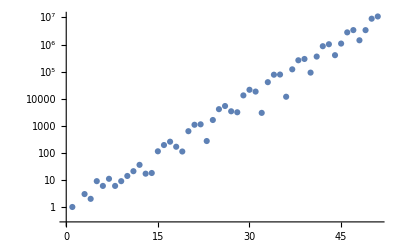

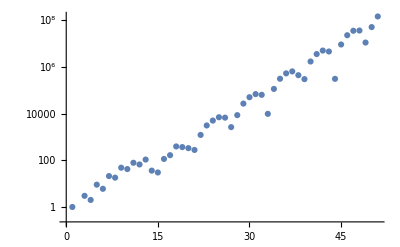

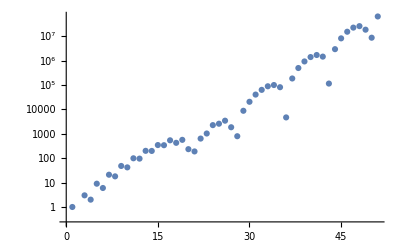

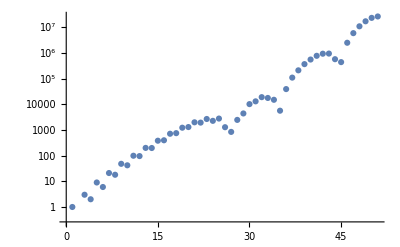

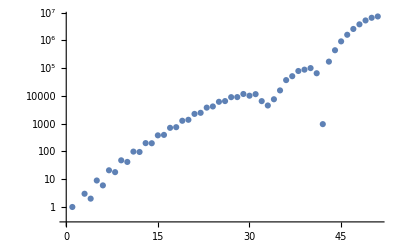

```mathematica
Do[
Print[ListLogPlot[CoefficientList[indexX["16",NN],x]]]
,
{NN,2,10,2}
]
```

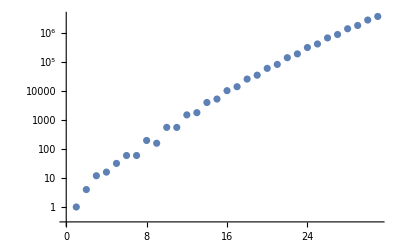

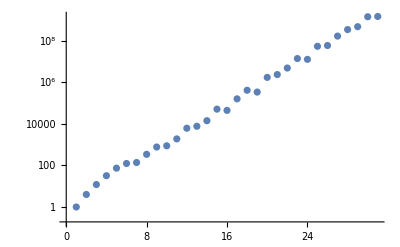

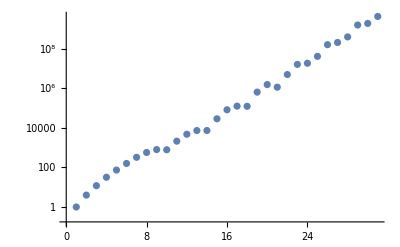

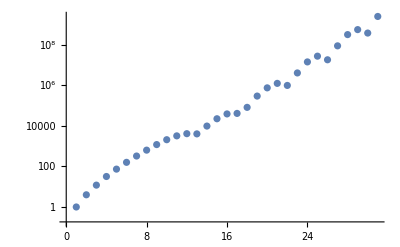

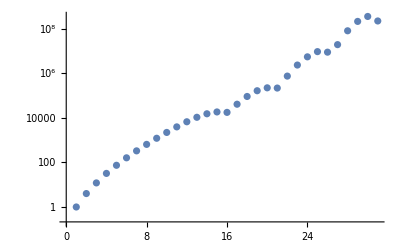

```mathematica
Do[
Print[ListLogPlot[CoefficientList[indexX["sx",NN],x]]]
,
{NN,2,10,2}
]
```

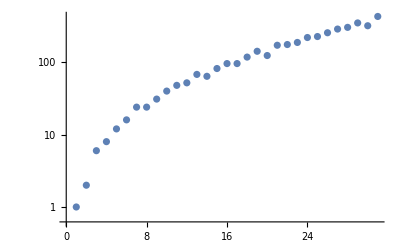

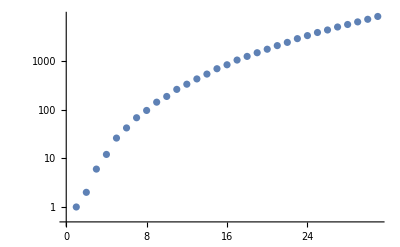

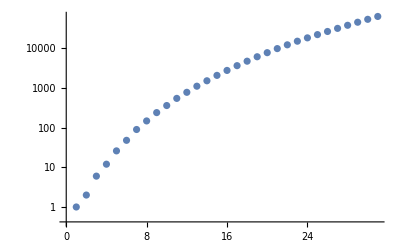

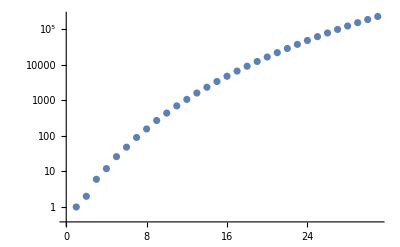

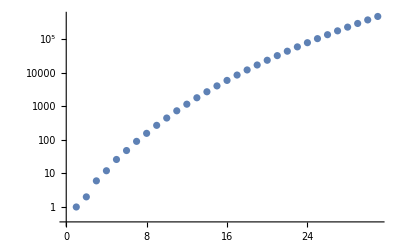

```mathematica
Do[
Print[ListLogPlot[CoefficientList[indexX["fm",NN],x]]]
,
{NN,2,10,2}
]
```

### Ratio U(N)

```mathematica
Series[indexGAP["fs",5],{x,0,4}]
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(3/b^3+1/b+b+3 b^3) x^3+(2+5/b^4+1/b^2+b^2+5 b^4) x^4+O[x]^5

```mathematica
Series[indexGAP["us",5],{x,0,4}]
```

1+2 x+4 x^2+8 x^3+14 x^4+O[x]^5

```mathematica
indexX["us",3]
```

1+2 x+4 x^2+8 x^3+9 x^4+14 x^5+20 x^6+24 x^7+30 x^8+34 x^9+46 x^10+52 x^11+60 x^12+70 x^13+76 x^14+88 x^15+102 x^16+120 x^17+118 x^18+136 x^19+154 x^20+160 x^21+184 x^22+200 x^23+208 x^24+234 x^25+252 x^26+244 x^27+295 x^28+308 x^29+308 x^30+360 x^31+374 x^32+368 x^33+420 x^34+444 x^35+422 x^36+494 x^37+528 x^38+520 x^39+567 x^40+602 x^41+580 x^42+660 x^43+696 x^44+656 x^45+752 x^46+784 x^47+748 x^48+860 x^49+900 x^50

```mathematica
indexX["fs",3]
```

1+2 x+4 x^2+8 x^3+9 x^4+14 x^5+20 x^6+24 x^7+30 x^8+34 x^9+46 x^10+52 x^11+60 x^12+70 x^13+76 x^14+88 x^15+102 x^16+120 x^17+126 x^18+136 x^19+154 x^20+160 x^21+184 x^22+200 x^23+224 x^24+234 x^25+252 x^26+244 x^27+295 x^28+308 x^29+340 x^30+360 x^31+374 x^32+396 x^33+420 x^34+444 x^35

```mathematica
Table[indexX["us",NN]-indexX["fs",NN]+O[x]^36,{NN,2,10}]
```

{O[x]^36,-8 x^18-16 x^24-32 x^30-28 x^33+O[x]^36,O[x]^36,O[x]^36,O[x]^36,O[x]^36,O[x]^36,O[x]^36,O[x]^36}

```mathematica
Clear[indexX];
Get[NotebookDirectory[]<>"indU.mx"];
Ratio[type_,NN_]:=CoefficientList[indexX[type,NN],x][[;;31]]/CoefficientList[indexX["us",NN],x][[;;31]];
```

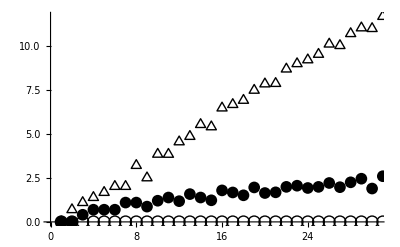

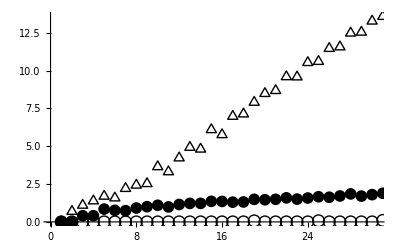

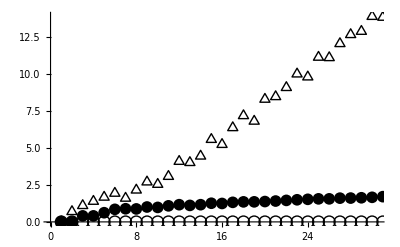

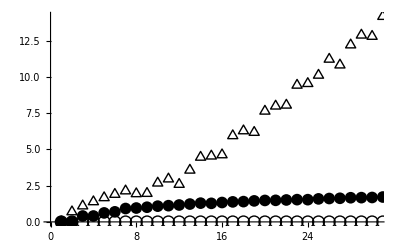

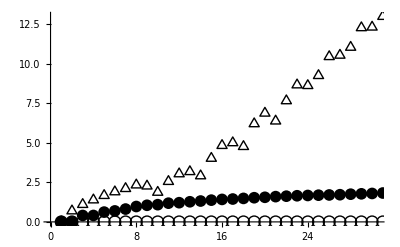

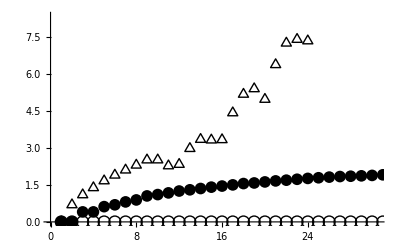

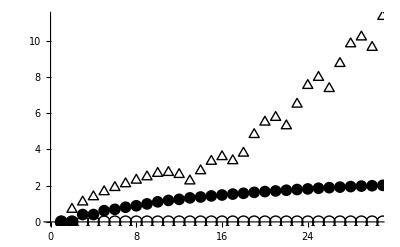

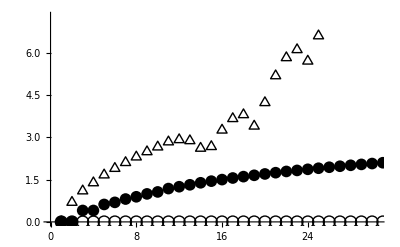

```mathematica
Do[
data=Table[Log[#]&/@Ratio[type,NN],{type,{"fs","fm","sx"}}];
plot=ListPlot[data,PlotRange->{{0,30.5},Automatic},
AxesLabel->{MaTeX["2h",Magnification->mag],MaTeX["\\log(|d|/|d_\\mathrm{FS}|)",Magnification->mag]},PlotLabel->MaTeX["\\mathrm{U}("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"○",size},{"●",size},{"△",size}}];
(*Export["/Users/yinhslin/git/schur/index/SU"<>ToString[NN]<>".pdf",plot];*)
Print[plot];
,
{NN,2,10,1}
]
```

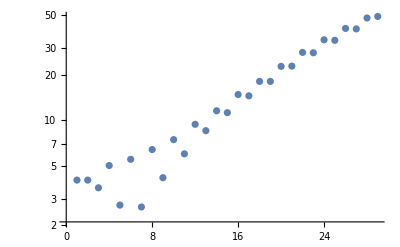

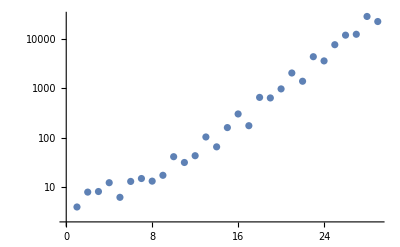

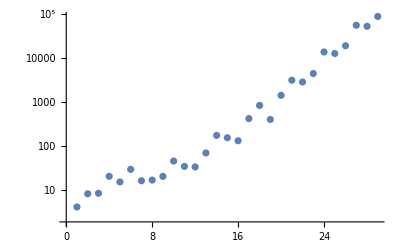

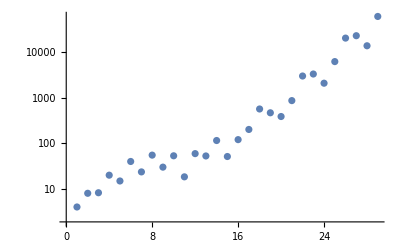

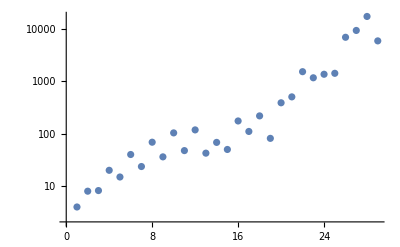

```mathematica
Do[
Print[ListLogPlot[Ratio[NN]]]
,
{NN,2,10,2}
]
```

```mathematica
Clear[indexX];
Get[NotebookDirectory[]<>"indU.mx"];
Ratio[NN_]:=CoefficientList[indexX["16",NN],x][[3;;36]]/CoefficientList[indexX["fs",NN],x][[3;;36]];
```

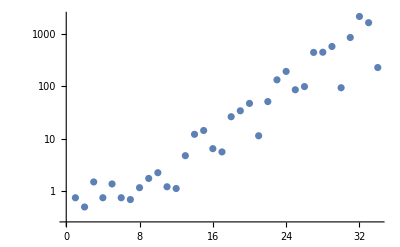

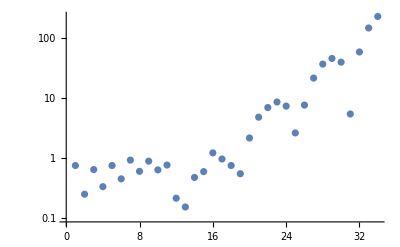

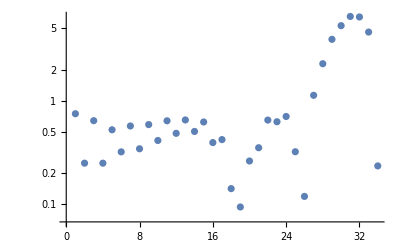

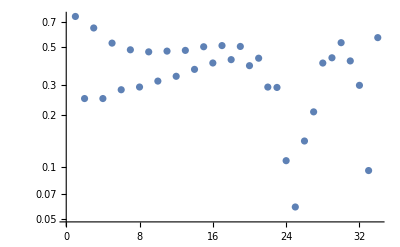

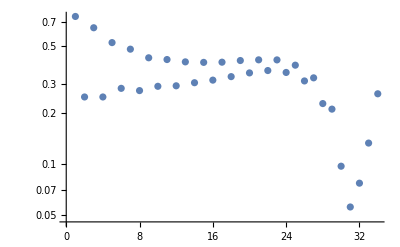

```mathematica
Do[
Print[ListLogPlot[Ratio[NN]]]
,
{NN,2,10,2}
]
```

```mathematica
Clear[indexX];
Get[NotebookDirectory[]<>"indU.mx"];
Ratio[NN_]:=CoefficientList[indexX["fm",NN],x][[3;;]]/CoefficientList[indexX["fs",NN],x][[3;;31]];
```

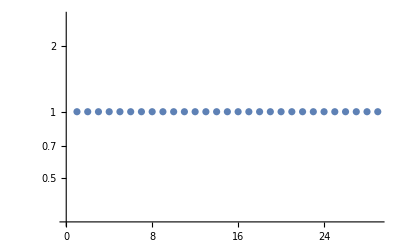

-Graphics-

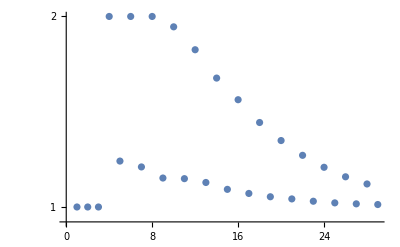

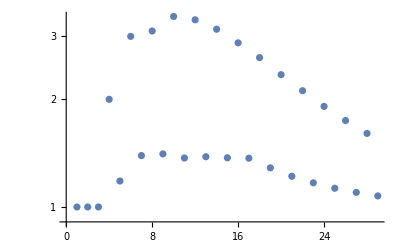

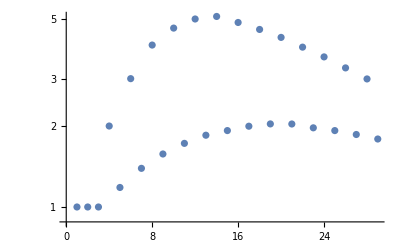

```mathematica
Do[
Print[ListLogPlot[Ratio[NN]]]
,
{NN,2,10,2}
]
```

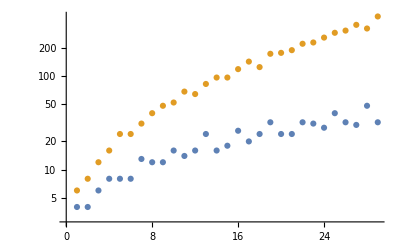

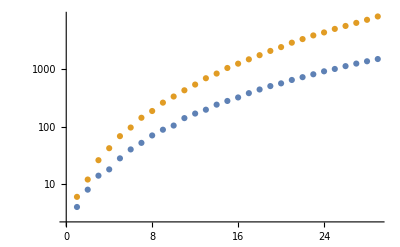

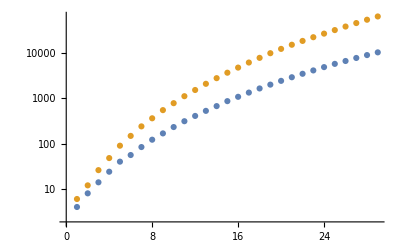

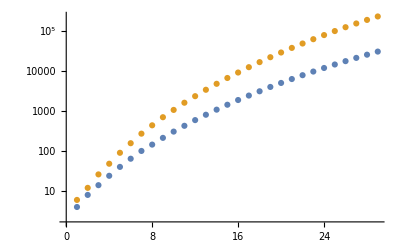

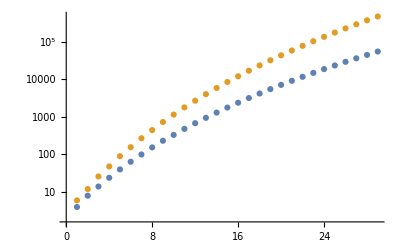

```mathematica
Do[
Print[ListLogPlot[{CoefficientList[indexX["fs",NN],x][[3;;31]],CoefficientList[indexX["fm",NN],x][[3;;31]]}]];
,
{NN,2,10,2}
]
```

### Ratio SU(N)

```mathematica
Clear[indexX];
Get[NotebookDirectory[]<>"ind.mx"];
Ratio[NN_]:=CoefficientList[indexX["fm",NN],x][[3;;]]/CoefficientList[indexX["fs",NN],x][[3;;31]];
```

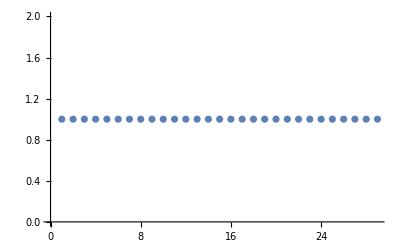

-Graphics-

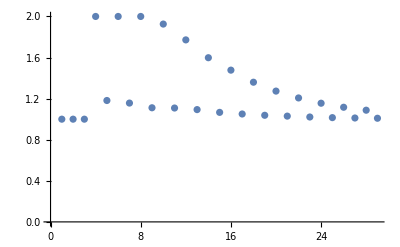

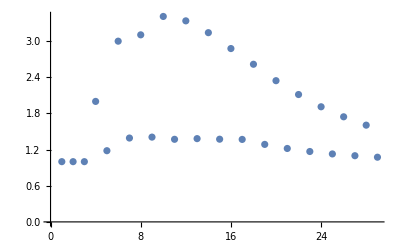

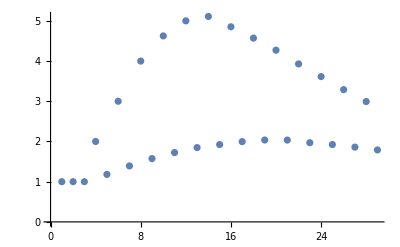

```mathematica
Do[
Print[ListPlot[Ratio[NN]]]
,
{NN,2,10,2}
]
```

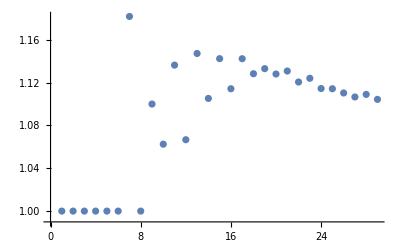

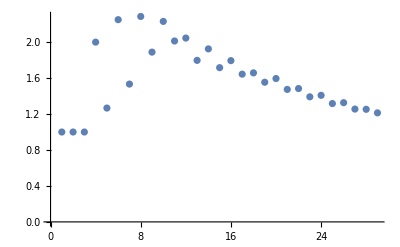

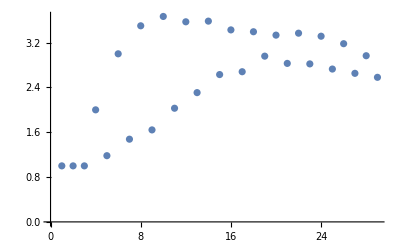

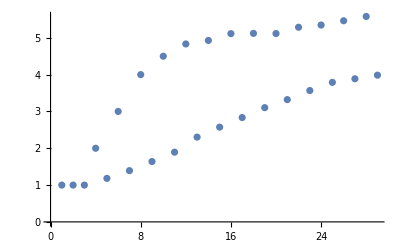

```mathematica
Do[
Print[ListPlot[Ratio[NN]]]
,
{NN,3,10,2}
]
```

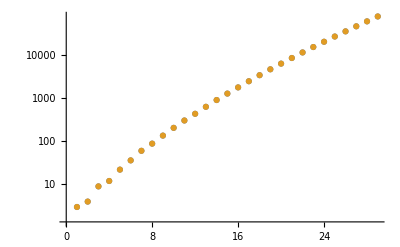

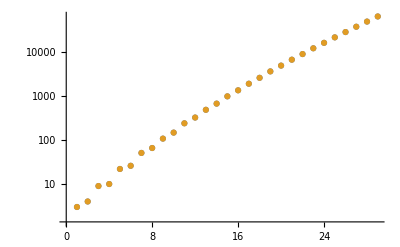

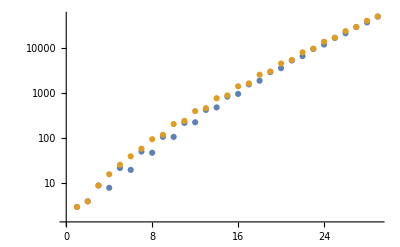

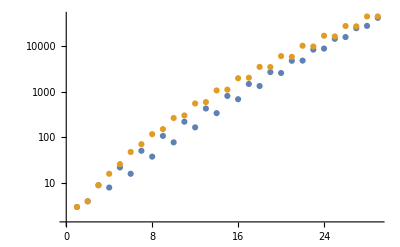

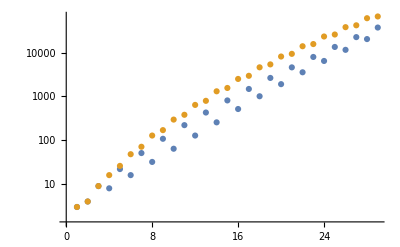

```mathematica
Do[
Print[ListLogPlot[{CoefficientList[indexX["fs",NN],x][[3;;31]],CoefficientList[indexX["fm",NN],x][[3;;31]]}]];
,
{NN,2,10,2}
]
```

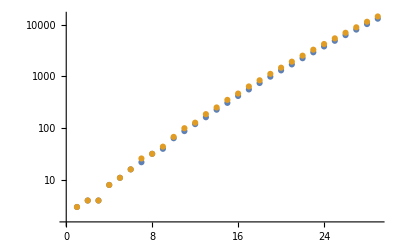

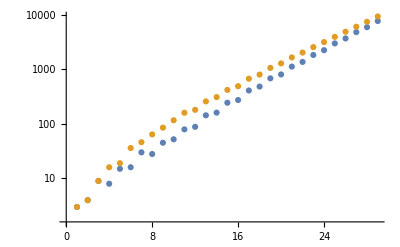

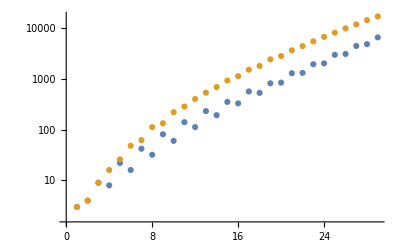

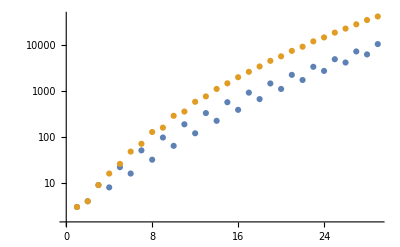

```mathematica
Do[
Print[ListLogPlot[{CoefficientList[indexX["fs",NN],x][[3;;31]],CoefficientList[indexX["fm",NN],x][[3;;31]]}]];
,
{NN,3,10,2}
]
```

### 1/16 unrefined index

```mathematica
Clear[SnChar];
SnChar[n_,NN_]:=SnChar[n,NN]=Module[{fn=NotebookDirectory[]<>"sn/"<>ToString[n]<>"_"<>ToString[NN]<>".m"},
If[FileExistsQ[fn],
Get[fn],
Print["Missing n="<>ToString[n]<>" N="<>ToString[NN]];
]
];
```

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}];
is[x_]:=1-((1-x^2)^3)/((1-x^3)^2);
indexGAP[N_,level_]:=Module[{snchar},
snchar=SnChar[level,N];
Sum[
Product[is[x^i],{i,P[[1]]}] 1/z[P[[1]]] P[[2]]
,{P,snchar}]
];
```

```mathematica
n=30;
AbsoluteTiming[Series[(1+Sum[indexGAP[2,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}]]
```

{8.01475,1+6 x^4-6 x^5-7 x^6+18 x^7+6 x^8-36 x^9+6 x^10+84 x^11-80 x^12-132 x^13+309 x^14-18 x^15-567 x^16+516 x^17+613 x^18-1392 x^19-180 x^20+2884 x^21-1926 x^22-4242 x^23+7890 x^24+792 x^25-15876 x^26+13804 x^27+15177 x^28-37536 x^29+7049 x^30+O[x]^31}

```mathematica
n=30;
AbsoluteTiming[Series[(1+Sum[indexGAP[3,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}]]
```

{7.97039,1+6 x^4-6 x^5+3 x^6+6 x^7-16 x^9+27 x^10+18 x^11-87 x^12+96 x^13+54 x^14-222 x^15+132 x^16+210 x^17-235 x^18-468 x^19+1284 x^20-534 x^21-2268 x^22+4392 x^23-1995 x^24-4128 x^25+6957 x^26-1288 x^27-5310 x^28-2376 x^29+22695 x^30+O[x]^31}

#### Timing test

```mathematica
NN=10;
Monitor[times=Table[AbsoluteTiming[
tmp=Series[(1+Sum[indexGAP[NN,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}];
tmp=Sum[Expand[SeriesCoefficient[tmp,{x,0,i}]]x^i,{i,0,n}]+O[x]^(n+1);][[1]],{n,0,30}];
,n]
```

```mathematica
times
```

{0.000183,0.000208,0.001361,0.001615,0.002252,0.002788,0.003967,0.005423,0.008955,0.024074,0.015569,0.021092,0.029499,0.044765,0.065688,0.085935,0.124216,0.185478,0.249346,0.365841,0.495764,0.704522,0.853088,1.27728,1.65177,2.02689,3.06127,3.9322,5.60944,7.31062,9.13204}

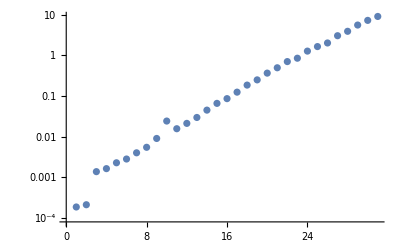

```mathematica
ListLogPlot[times]
```

### unflavored Schur index

```mathematica
Clear[SnChar];
SnChar[n_,NN_]:=SnChar[n,NN]=Module[{fn=NotebookDirectory[]<>"sn/"<>ToString[n]<>"_"<>ToString[NN]<>".m"},
If[FileExistsQ[fn],
Get[fn],
Print["Missing n="<>ToString[n]<>" N="<>ToString[NN]];
]
];
```

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}];
is[x_]:=1-(1-x)^2/(1-x^2);
indexGAP[N_,level_]:=Module[{snchar},
snchar=SnChar[level,N];
Sum[
Product[is[x^i],{i,P[[1]]}] 1/z[P[[1]]] P[[2]]
,{P,snchar}]
];
```

```mathematica
n=15;
Series[(1+Sum[indexGAP[3,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}]
```

1+3 x^2+4 x^4+7 x^6+6 x^8+12 x^10+8 x^12+15 x^14+O[x]^16

#### Timing test

```mathematica
NN=10;
Monitor[times=Table[AbsoluteTiming[
tmp=Series[(1+Sum[indexGAP[NN,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}];
tmp=Sum[Expand[SeriesCoefficient[tmp,{x,0,i}]]x^i,{i,0,n}]+O[x]^(n+1);][[1]],{n,0,15}];
,n]
```

```mathematica
times
```

{0.000664,0.022886,0.004359,0.004527,0.007984,0.046521,0.021452,0.024772,0.040875,0.054079,0.116588,0.229074,0.512166,0.805612,1.63121,2.73223}

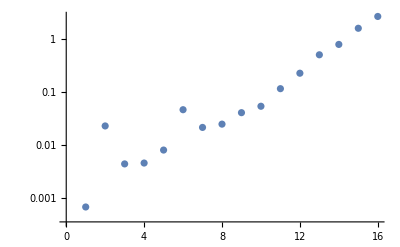

```mathematica
ListLogPlot[times]
```

### flavored Schur index

```mathematica
Clear["Global`*"];
SnChar[n_,NN_]:=SnChar[n,NN]=Module[{fn=NotebookDirectory[]<>"sn/"<>ToString[n]<>"_"<>ToString[NN]<>".m"},
If[FileExistsQ[fn],
Get[fn],
Print["Missing n="<>ToString[n]<>" N="<>ToString[NN]];
]
];
```

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}];
is[x_,b_]:=1-((1-b x)(1-b^-1 x))/(1-x^2);
indexGAP[N_,level_]:=Module[{snchar},
snchar=SnChar[level,N];
Sum[
Product[is[x^i,b^i],{i,P[[1]]}] 1/z[P[[1]]] P[[2]]
,{P,snchar}]
];
```

```mathematica
n=15;
Timing[tmp=Series[(1+Sum[indexGAP[3,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}]][[1]]
Timing[tmp=Sum[Expand[SeriesCoefficient[tmp,{x,0,i}]]x^i,{i,0,n}]+O[x]^(n+1)][[1]]
```

0.559317

2.2246

```mathematica
coefs=Total[Abs[CoefficientList[If[#=!=0,b^Exponent[#,b]*#,0],b]]]&/@Expand[CoefficientList[tmp,x]];
coefs.Table[x^n,{n,0,Length[coefs]-1}]
```

1+3 x^2+4 x^3+4 x^4+8 x^5+11 x^6+16 x^7+22 x^8+32 x^9+40 x^10+64 x^11+88 x^12+120 x^13+163 x^14+228 x^15

#### Timing test

```mathematica
NN=10;
Monitor[times=Table[AbsoluteTiming[
tmp=Series[(1+Sum[indexGAP[NN,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}];
tmp=Sum[Expand[SeriesCoefficient[tmp,{x,0,i}]]x^i,{i,0,n}]+O[x]^(n+1);][[1]],{n,0,15}];
,n]
```

```mathematica
times
```

{0.000664,0.022886,0.004359,0.004527,0.007984,0.046521,0.021452,0.024772,0.040875,0.054079,0.116588,0.229074,0.512166,0.805612,1.63121,2.73223}

```mathematica
ListLogPlot[times]
```

-Graphics-

### flavored MacDonald

```mathematica
Clear["Global`*"];
SnChar[n_,NN_]:=SnChar[n,NN]=Module[{fn=NotebookDirectory[]<>"sn/"<>ToString[n]<>"_"<>ToString[NN]<>".m"},
If[FileExistsQ[fn],
Get[fn],
Print["Missing n="<>ToString[n]<>" N="<>ToString[NN]];
]
];
```

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}];
is[x_,b_,s_]:=1-((1-b s x)(1-b^-1 s x))/(1-x^2);
indexGAP[N_,level_]:=Module[{snchar},
snchar=SnChar[level,N];
Sum[
Product[is[x^i,b^i,s^i],{i,P[[1]]}] 1/z[P[[1]]] P[[2]]
,{P,snchar}]
];
```

```mathematica
n=15;
Timing[tmp=Series[(1+Sum[indexGAP[3,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}]][[1]]
Timing[tmp=Sum[Expand[SeriesCoefficient[tmp,{x,0,i}]]x^i,{i,0,n}]+O[x]^(n+1)][[1]]
```

1.31428

7.37201

```mathematica
coefs=Total[Abs[CoefficientList[If[#=!=0,b^Exponent[#,b]*s^Exponent[#,s]#,0],{b,s}]//Flatten]]&/@Expand[CoefficientList[tmp,x]];
coefs.Table[x^n,{n,0,Length[coefs]-1}]
```

1+3 x^2+4 x^3+4 x^4+8 x^5+11 x^6+16 x^7+26 x^8+32 x^9+44 x^10+68 x^11+100 x^12+128 x^13+187 x^14+252 x^15

#### Timing test

```mathematica
NN=10;
Monitor[times=Table[AbsoluteTiming[
tmp=Series[(1+Sum[indexGAP[NN,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}];
tmp=Sum[Expand[SeriesCoefficient[tmp,{x,0,i}]]x^i,{i,0,n}]+O[x]^(n+1);][[1]],{n,0,15}];
,n]
```

```mathematica
times
```

{0.000401,0.003377,0.00479,0.008032,0.036389,0.033174,0.035306,0.055094,0.106958,0.214232,0.420189,0.800046,1.5113,2.73818,4.9247,8.59801}

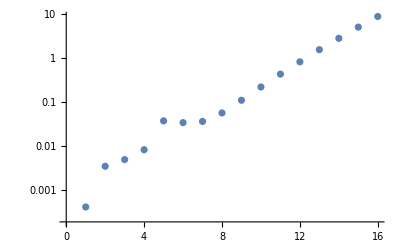

```mathematica
ListLogPlot[times]
```

### flavored Schur index (TODO)

```mathematica
Clear["Global`*"];
SnChar[n_,NN_]:=SnChar[n,NN]=Module[{fn=NotebookDirectory[]<>"sn/"<>ToString[n]<>"_"<>ToString[NN]<>".m"},
If[FileExistsQ[fn],
Get[fn],
Print["Missing n="<>ToString[n]<>" N="<>ToString[NN]];
]
];
```

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}];
(*is[x_,b_]:=is[x,b]=1-((1-b x)(1-b^-1 x))/(1-x^2);*)
is[cut_][x_,b_]:=is[cut][x,b]=Series[1-((1-b x)(1-b^-1 x))/(1-x^2),{x,0,cut}];
is[cut_][i_][x_,b_]:=is[cut][i][x,b]=Series[Normal[Series[is[cut][x,b],{x,0,Floor[cut/i]}]]/.{x->x^i,b->b^i},{x,0,cut}];
indexGAP[cut_][N_,level_][x_,b_]:=Module[{snchar},
snchar=SnChar[level,N];
Sum[
Product[is[cut][i][x,b],{i,P[[1]]}] 1/z[P[[1]]] P[[2]]
,{P,snchar}]
];
```

```mathematica
n=15;
Timing[tmp=Series[(1+Sum[indexGAP[n][3,i][x,b],{i,1,n}])/(1+Sum[indexGAP[n][1,i][x,b],{i,1,n}]),{x,0,n}]][[1]]
Timing[tmp=Sum[Expand[SeriesCoefficient[tmp,{x,0,i}]]x^i,{i,0,n}]+O[x]^(n+1)][[1]]
```

10.6937

6.25687

```mathematica
coefs=Total[Abs[CoefficientList[If[#=!=0,b^Exponent[#,b]*#,0],b]]]&/@Expand[CoefficientList[tmp,x]];
coefs.Table[x^n,{n,0,Length[coefs]-1}]
```

1+3 x^2+4 x^3+4 x^4+8 x^5+11 x^6+16 x^7+22 x^8+32 x^9+40 x^10+64 x^11+88 x^12+120 x^13+163 x^14+228 x^15

```mathematica
NN=3;
Monitor[times=Table[AbsoluteTiming[
tmp=Series[(1+Sum[indexGAP[NN,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}];
tmp=Sum[Expand[SeriesCoefficient[tmp,{x,0,i}]]x^i,{i,0,n}]+O[x]^(n+1);][[1]],{n,0,20}];
,n]
```

```mathematica
times
```

{0.000385,0.005231,0.003296,0.004997,0.015982,0.011472,0.009223,0.009586,0.018855,0.036239,0.082976,0.278406,0.501553,0.916047,1.64093,2.93195,5.39749,8.54385,18.6088,36.0703,63.858}

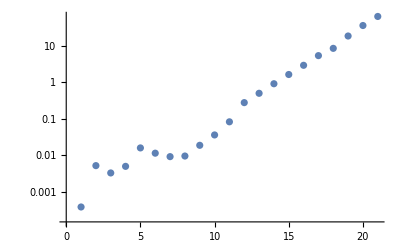

```mathematica
ListLogPlot[times]
```

### Log(d)/N^2 plots

```mathematica
Clear[indexX];
Get[NotebookDirectory[]<>"ind.mx"];
Ratio[NN_]:=CoefficientList[indexX["fm",NN],x][[3;;]]/CoefficientList[indexX["fs",NN],x][[3;;31]];
```

```mathematica
<<MaTeX`;
texStyle={FontFamily->"Latin Modern Roman",FontSize->14};
SetOptions[ListPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}(*,PlotStyle->Black*)];
size = 12;
mag = 2;
```

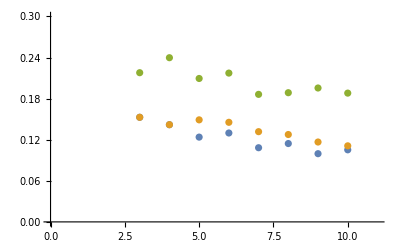

```mathematica
ListPlot[{Table[{i,(Interpolation[CoefficientList[indexX["fs",i],x][[3;;]]//Abs//Log][i^2/(100/30)-1])/i^2},{i,3,10}],Table[{i,(Interpolation[CoefficientList[indexX["fm",i],x][[3;;]]//Abs//Log][i^2/(100/30)-1])/i^2},{i,3,10}],Table[{i,(Interpolation[CoefficientList[indexX["sx",i],x][[3;;]]//Abs//Log][i^2/(100/30)-1])/i^2},{i,3,10}]},PlotRange->{{0,11},{0,0.3}},
AxesLabel->{MaTeX["N",Magnification->mag],MaTeX["\\log(|d|)/N^2",Magnification->mag]}
]
```

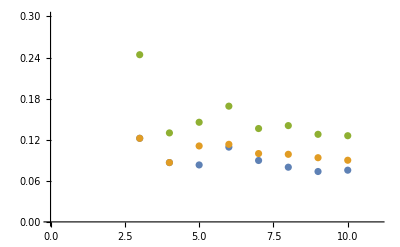

```mathematica
ListPlot[{Table[{i,Log[Coefficient[indexX["fs",i],x^Round[i^2/(144/30)]]//Abs]/i^2},{i,3,12}],Table[{i,Log[Coefficient[indexX["fm",i],x^Round[i^2/(144/30)]]//Abs]/i^2},{i,3,12}],Table[{i,Log[Coefficient[indexX["sx",i],x^Round[i^2/(144/30)]]//Abs]/i^2},{i,3,12}]},PlotRange->{{0,11},{0,0.3}}]
```

### Junk

```mathematica
(*SnChar[n_,NN_]:=Module[{},
script="LoadPackage( \"ctbllib\" );;
	SnChar := function(n, N)
	\tlocal ct, irr, cp, short, part, sq, ans;
	\tct := CharacterTable(\"Symmetric\", n);;
	\tirr := Irr(ct);;
	\tcp := ClassParameters(ct);;
	\tshort := Filtered([1..Length(cp)], x->Length(cp[x][2]) <= N);;
	\tpart := List(cp, x -> x[2]);;
	\tsq := Sum(short, x -> irr[x] * irr[x]);;
	\tans := List([1..Length(part)], x -> [part[x], sq[x]]);;
	\tPrintTo(\"/Users/yinhslin/Downloads/index/output.txt\", ans);;
	end;;";
	script=script<>"
	SnChar("<>ToString[n]<>","<>ToString[NN]<>");;";

Export[NotebookDirectory[]<>"sym.txt",script];
DeleteFile[NotebookDirectory[]<>"sym.g"];
RenameFile[NotebookDirectory[]<>"sym.txt",NotebookDirectory[]<>"sym.g"];
gap="/Users/yinhslin/Downloads/gap-4.12.2/gap";
Run[gap<>" -q < "<>NotebookDirectory[]<>"sym.g"];

output=Import[NotebookDirectory[]<>"output.txt"];
output=StringReplace[output,{"["->"{","]"->"}"}]//ToExpression;
output
];*)
```

## GroupMath

```mathematica
<<GroupMath`
```

paclet:GroupMath/tutorial/GroupMathDoc | XXXXXXXXXXXXXXXXXXXXXXXXXXX GroupMath XXXXXXXXXXXXXXXXXXXXXXXXXXVersion: 1.1.2 (6/May/2020)Author: Renato FonsecaReference: 2011.01764 [hep-th]Website: http://renatofonseca.net/groupmathBuilt-in documentation: paclet:GroupMath/tutorial/GroupMathDocXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX

SetDelayed::write: Tag BlockDiagonalMatrix in BlockDiagonalMatrix[blocks_] is Protected.

### Sn characters complexity analysis

```mathematica
partitions=IntegerPartitions[30];
shortPartitions=Select[partitions,Length[#]<=5&];
```

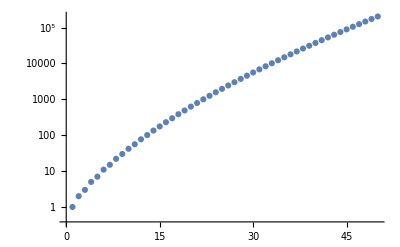

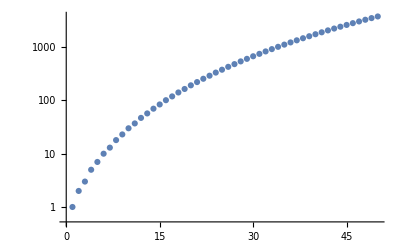

```mathematica
ListLogPlot[Table[Length[IntegerPartitions[n]],{n,1,50}]]
ListLogPlot[Table[Length[Select[IntegerPartitions[n],Length[#]<=5&]],{n,1,50}]]
```

### 1/16 unrefined index

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}]
is[x_]:=1-((1-x^2)^3)/((1-x^3)^2)
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,P}] 1/z[P]
SnClassCharacter[λ,P]^2
,{λ,shortPartitions},{P,partitions}]
]
```

```mathematica
n=18;
Series[Sum[index[2,i],{i,1,n}],{x,0,2n+1}]
```

3 x^2-2 x^3+9 x^4-6 x^5+11 x^6-6 x^7+9 x^8+14 x^9-21 x^10+36 x^11-17 x^12-18 x^13+114 x^14-194 x^15+258 x^16-168 x^17-112 x^18+630 x^19-1089 x^20+1130 x^21-273 x^22-1632 x^23+4104 x^24-5364 x^25+3426 x^26+3152 x^27-13233 x^28+21336 x^29-18319 x^30-2994 x^31+40752 x^32-76884 x^33+78012 x^34-11808 x^35-121384 x^36+262206 x^37+O[x]^38

```mathematica
n=18;
Series[Sum[index[3,i],{i,1,n}],{x,0,2n+1}]
```

3 x^2-2 x^3+9 x^4-6 x^5+21 x^6-18 x^7+33 x^8-22 x^9+36 x^10+6 x^11-19 x^12+90 x^13-99 x^14+138 x^15-9 x^16-210 x^17+672 x^18-1116 x^19+1554 x^20-1270 x^21-36 x^22+2898 x^23-6705 x^24+10224 x^25-9918 x^26+2018 x^27+16470 x^28-42918 x^29+66906 x^30-66006 x^31+13566 x^32+106404 x^33-273204 x^34+407442 x^35-364710 x^36-12024 x^37+O[x]^38

### unflavored Schur index

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}]
is[x_]:=1-(1-x)^2/(1-x^2)
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,P}] 1/z[P]
SnClassCharacter[λ,P]^2
,{λ,shortPartitions},{P,partitions}]
]
```

```mathematica
n=16;
Series[(1+Sum[index[2,i],{i,1,n}])/(1+Sum[index[1,i],{i,1,n}]),{x,0,n}]
```

1+3 x^2-4 x^3+9 x^4-12 x^5+22 x^6-36 x^7+60 x^8-88 x^9+135 x^10-204 x^11+302 x^12-432 x^13+627 x^14-900 x^15+1269 x^16+O[x]^17

```mathematica
n=10;
Series[(1+Sum[index[7,i],{i,1,n}])/(1+Sum[index[1,i],{i,1,n}]),{x,0,n}]
```

1+3 x^2+9 x^4+22 x^6+42 x^8+81 x^10+O[x]^11

## Mathematica built in FiniteGroupData

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}]
is[x_]:=1-((1-x^2)^3)/((1-x^3)^2)
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,partitions[[k]]}] 1/z[partitions[[k]]]
FiniteGroupData[{"SymmetricGroup",level},"CharacterTable"][[j,Length[partitions]-k+1]]^2
,{j,1,Length[shortPartitions]},{k,1,Length[partitions]}]
]
```

```mathematica
Series[Sum[index[2,i],{i,1,10}],{x,0,12}]
```

3 x^2-2 x^3+9 x^4-6 x^5+11 x^6-6 x^7+9 x^8+14 x^9-21 x^10+36 x^11+81 x^12+O[x]^13

```mathematica
FiniteGroupData[{"SymmetricGroup",11},"CharacterTable"]
```

Missing[NotAvailable]

## Direct input

```mathematica
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,partitions[[k]]}] 1/z[partitions[[k]]]
χ[shortPartitions[[j]],partitions[[k]]]^2
,{j,1,Length[shortPartitions]},{k,1,Length[partitions]}]
]
 χ[{1},{1}]=1;
 χ[{1,1},{1,1}]=1;
 χ[{1,1},{2}]=-1;
 χ[{2},{1,1}]=1;
χ[{2},{2}]=1;
χ[{1,1,1},{1,1,1}]=1;
χ[{1,1,1},{2,1}]=-1;
χ[{1,1,1},{3}]=1;
χ[{2,1},{1,1,1}]=2;
χ[{2,1},{2,1}]=0;
χ[{2,1},{3}]=-1;
χ[{3},{1,1,1}]=1;
χ[{3},{2,1}]=1;
χ[{3},{3}]=1;
```